```mathematica
BlueC=RGBColor[0.2627,0.4313,1];
PurpleC=RGBColor[0.5411,0.0784,0.9607];
RedC=RGBColor[0.60,0.30,0];
```

# Energy divider coupling

```mathematica
Ns=3;p=2;q=1;
```

```mathematica
Ns=4;p=3;q=1;
```

```mathematica
Ns=5;p=4;q=1;
```

```mathematica
Ns=6;p=5;q=1;
```

```mathematica
Ns=5;p=2;q=1;
```

```mathematica
Ns=7;p=2;q=1;
```

```mathematica
Ns=4;p=3;q=2;
```

```mathematica
Ns=5;p=4;q=2;
```

1. The system has two TLSs coupled each to a thermal bath.
2. The energy levels of the two levels are not necessarily resonant (may be significantly off-resonant).
3. A harmonic oscillator mediates the thermal flow between the two TLSs.

## System Hamiltonians

Identity operator

```mathematica
Id[ve_,ho_]:=ve,ho
```

### Subsystem Hamiltonians

The system contains three subsystems L, M and R. 
L and R are two level systems. M is a harmonic oscillator.

The non-interacting part of the system Hamiltonian may be written,

(Ĥ)_sys^0 = ℏ ω_L (Ŝ)_z^L + ℏ ω_M M̂†M̂ + ℏ ω_R (Ŝ)_z^R

#### Truncated Hamiltonian

With a full harmonic oscillator in the subsystem M and two TLSs in L and R, the dimensionality of the combined system density matrix is 2×∞×2.
Being an infinite dimensional system, we cannot apply matrix methods to solve for system dynamics.

To resolve this issue, we truncate the harmonic oscillator at level N, assuming that levels higher than N are scarcely occupied. This is justified since for low temperatures, the dissipation terms for subsystems L and R would tend to drive the state of M towards low energy states.

Once harmonic oscillator is truncated to N levels only,

(Ĥ)_sys^0 = ℏ ω_L (Ŝ)_z^L + ∑_(m=0)^N ℏ ω_M m |m><m| + ℏ ω_R (Ŝ)_z^R

To further simplify the Hamiltonian, we shift the zero-reference of the energy levels to the lowest |g_L,0_M,g_R> state.

(Ĥ)_sys^0 = ℏ ω_L (1 | 0
0 | 0)^L + ∑_(m=0)^N ℏ ω_M m |m><m| + ℏ ω_R (1 | 0
0 | 0)^R

```mathematica
HLSep[veL_,hoL_,veM_,hoM_,veR_,hoR_]:=({{ℏ Subscript[ω, 1], 0}, {0, 0}})[[veL,hoL]]Id[veM,hoM]Id[veR,hoR]
```

```mathematica
HMSep[veL_,hoL_,veM_,hoM_,veR_,hoR_]:=Id[veL,hoL](ℏ Subscript[ω, M](Ns-veM)veM,hoM)Id[veR,hoR]
```

```mathematica
HRSep[veL_,hoL_,veM_,hoM_,veR_,hoR_]:=Id[veL,hoL]Id[veM,hoM]({{ℏ Subscript[ω, 2], 0}, {0, 0}})[[veR,hoR]]
```

The total number of system eigenstates is then 2×N×2 = 4N.

In the matrix representation, the highest energy state |e,N,e> is given the first place, and the lowest energy state |g,0,g> is given the last space. 

For example,
|1>	= |e,N-1,e>
|2>	= |e,N-1,g>
|3>	= |e,N-2,e>
|4>	= |e,N-2,g>
....
|4N-3>	= |g,1,e>
|4N-2>	= |g,1,g>
|4N-1>	= |g,0,e>
|4N>	= |g,0,g>

Eigenstate mapping function, maps overall state (1 to 4N) to subsystem L, M, R state,

```mathematica
EmapL[i_]:=Quotient[i-1,2Ns]+1
EmapM[i_]:=Quotient[QuotientRemainder[i-1,2Ns][[2]],2]+1
EmapR[i_]:=QuotientRemainder[i-1,2][[2]]+1
```

```mathematica
Table[EmapL[i],{i,1,4Ns}]
Table[EmapM[i],{i,1,4Ns}]
Table[EmapR[i],{i,1,4Ns}]
```

{1,1,1,1,1,1,2,2,2,2,2,2}

{1,1,2,2,3,3,1,1,2,2,3,3}

{1,2,1,2,1,2,1,2,1,2,1,2}

Matrix form of the three Hamiltonians

```mathematica
HL[ve_,ho_]:=HLSep[EmapL[ve],EmapL[ho],EmapM[ve],EmapM[ho],EmapR[ve],EmapR[ho]]
HM[ve_,ho_]:=HMSep[EmapL[ve],EmapL[ho],EmapM[ve],EmapM[ho],EmapR[ve],EmapR[ho]]
HR[ve_,ho_]:=HRSep[EmapL[ve],EmapL[ho],EmapM[ve],EmapM[ho],EmapR[ve],EmapR[ho]]
```

Non-interacting subsystem Hamiltonians as a matrix in the combined system space

```mathematica
Hsys0Matrix = Table[HL[ve,ho]+HM[ve,ho]+HR[ve,ho],{ve,1,4Ns},{ho,1,4Ns}];
MatrixForm[Hsys0Matrix]
```

(ℏ ω_1+ℏ ω_2+2 ℏ ω_M | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ℏ ω_1+2 ℏ ω_M | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ℏ ω_1+ℏ ω_2+ℏ ω_M | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ℏ ω_1+ℏ ω_M | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ℏ ω_1+ℏ ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ℏ ω_1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ℏ ω_2+2 ℏ ω_M | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ℏ ω_M | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ ω_2+ℏ ω_M | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ ω_M | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ ω_2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Pauli matrices

### In z-base representation

|+z>=(1,0)
|-z>=(0,1)

```mathematica
Subscript[σ, axis_][ve_,ho_]:=axis,1({{0, 1}, {1, 0}})[[ve,ho]]+axis,2({{0, -ⅈ}, {ⅈ, 0}})[[ve,ho]]+axis,3({{1, 0}, {0, -1}})[[ve,ho]];
σP[ve_,ho_]:=1/2(Subscript[σ, 1][ve,ho]+ⅈ Subscript[σ, 2][ve,ho])
σM[ve_,ho_]:=1/2(Subscript[σ, 1][ve,ho]-ⅈ Subscript[σ, 2][ve,ho])

Subscript[σMatrix, axis_]:= Table[Subscript[σ, axis][ve,ho],{ve,1,2},{ho,1,2}]
σPMatrix:= Table[σP[ve,ho],{ve,1,2},{ho,1,2}]
σMMatrix:= Table[σM[ve,ho],{ve,1,2},{ho,1,2}]
```

```mathematica
{Subscript[σMatrix, 1],Subscript[σMatrix, 2],Subscript[σMatrix, 3],σPMatrix,σMMatrix};
Map[MatrixForm,%,1]
```

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1),(0 | 1
0 | 0),(0 | 0
1 | 0)}

### In compound system representation

```mathematica
Subscript[σ, P_,axis_][ve_,ho_]:=
P,1(Subscript[σ, axis][EmapL[ve],EmapL[ho]]Id[EmapM[ve],EmapM[ho]]Id[EmapR[ve],EmapR[ho]])+
P,2(Id[EmapL[ve],EmapL[ho]]Id [EmapM[ve],EmapM[ho]]Subscript[σ, axis][EmapR[ve],EmapR[ho]])

Subscript[σMatrix, P_,axis_]:=Table[Subscript[σ, P,axis][ve,ho],{ve,1,4Ns},{ho,1,4Ns}]
Subscript[σPMatrix, P_]:=1/2(Subscript[σMatrix, P,1]+ⅈ Subscript[σMatrix, P,2])
Subscript[σMMatrix, P_]:=1/2(Subscript[σMatrix, P,1]-ⅈ Subscript[σMatrix, P,2])
```

```mathematica
{MatrixForm[Subscript[σMatrix, 1,1]],MatrixForm[Subscript[σMatrix, 2,1]]}
```

{(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}

## Interaction Hamiltonian between the subsystems

The interactions between the subsystems are considered WEAK enough that the local master equation approach is justified.
This effectively means that the subsystem interactions should not significantly change the energy levels of the non-interacting Hamiltonian.

The energy levels of the individual components are specially tuned in our model. 
	1. First of all, there are no direct interactions between L and R.
	2. The energy levels are prepared so that
		ω_L≃p ω_M
		ω_R≃q ω_M
	3. Therefore the interactions are such that
		a) TLS L jumps up from |g_L> to |e_L> while the HO jumps down p steps from |(m+p)_M> to |m_M> (and vice versa).
		b) TLS R jumps up from |g_R> to |e_R> while the HO jumps down q steps from |(m+q)_M> to |m_M> (and vice versa).
	3. The interaction strengths between subsystems are given by γ_LM[m] and γ_MR[m] where m enumerates the different start (or end) state of the HO.

(Ĥ)_sys^1 = ∑_(m=0)^∞ ℏ γ_LM[m] (|e_L><g_L|⊗|m_M><(m+p)_M| + |g_L><e_L|⊗|(m+p)_M><m_M|)
	 +∑_(m=0)^∞ ℏ γ_MR[m] (|m_M><(m+q)_M|⊗|e_R><g_R| + |(m+q)_M><m_M|⊗|g_R><e_R|)

With the truncation of the HO at N, we have

(Ĥ)_sys^1 = ∑_(m=0)^(N-1-p) ℏ γ_LM[m] (|e_L><g_L|⊗|m_M><(m+p)_M| + |g_L><e_L|⊗|(m+p)_M><m_M|)
	 +∑_(m=0)^(N-1-q) ℏ γ_MR[m] (|m_M><(m+q)_M|⊗|e_R><g_R| + |(m+q)_M><m_M|⊗|g_R><e_R|)

Define some necessary matrices

|m_M><n_M| = OneMatrix[Ns-m,Ns-n,Ns]

```mathematica
OneMatrix[ve_,ho_,n_]:=Table[ve,i ho,j,{i,1,n},{j,1,n}]
OneMatrix[Ns-0,Ns-2,Ns]//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
1 | 0 | 0)

Considering the above Hamiltonian, we write the interaction between L and M as,

```mathematica
HintLM[ve_,ho_]:=(∑_(m=0)^(Ns-1-p) ℏ γLM[m]KroneckerProduct[(KroneckerProduct[σPMatrix,OneMatrix[Ns-m,Ns-(m+p),Ns]]+KroneckerProduct[σMMatrix,OneMatrix[Ns-(m+p),Ns-m,Ns]]),IdentityMatrix[2]])[[ve,ho]]
```

Similarly, we write the interaction between M and R as,

```mathematica
HintMR[ve_,ho_]:=(∑_(m=0)^(Ns-1-q) ℏ γMR[m]KroneckerProduct[IdentityMatrix[2],(KroneckerProduct[OneMatrix[Ns-m,Ns-(m+q),Ns],σPMatrix]+KroneckerProduct[OneMatrix[Ns-(m+q),Ns-m,Ns],σMMatrix])])[[ve,ho]]
```

Interacting system Hamiltonian as a matrix in the combined system space

```mathematica
Hsys1Matrix = Table[HintLM[ve,ho]+HintMR[ve,ho],{ve,1,4Ns},{ho,1,4Ns}];
MatrixForm[Hsys1Matrix]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ℏ γMR[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ℏ γMR[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ℏ γMR[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ℏ γMR[0] | 0 | 0 | ℏ γLM[0] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γLM[0] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ℏ γLM[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ℏ γLM[0] | 0 | 0 | ℏ γMR[1] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γMR[1] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γMR[0] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γMR[0] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Combined system Hamiltonian

(Ĥ)_sys = (Ĥ)_sys^0 + (Ĥ)_sys^1

```mathematica
HsysMatrix=Hsys0Matrix+Hsys1Matrix;
MatrixForm[HsysMatrix]
```

(ℏ ω_1+ℏ ω_2+2 ℏ ω_M | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ℏ ω_1+2 ℏ ω_M | ℏ γMR[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ℏ γMR[1] | ℏ ω_1+ℏ ω_2+ℏ ω_M | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ℏ ω_1+ℏ ω_M | ℏ γMR[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ℏ γMR[0] | ℏ ω_1+ℏ ω_2 | 0 | ℏ γLM[0] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ℏ ω_1 | 0 | ℏ γLM[0] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ℏ γLM[0] | 0 | ℏ ω_2+2 ℏ ω_M | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ℏ γLM[0] | 0 | 2 ℏ ω_M | ℏ γMR[1] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γMR[1] | ℏ ω_2+ℏ ω_M | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ ω_M | ℏ γMR[0] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γMR[0] | ℏ ω_2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### Visualize the energy levels of the combined system

```mathematica
unitassum={ℏ->1};
```

#### Bare energy levels without the interaction Hamiltonian

Raw eigensystem from Mathematica are not properly ordered

```mathematica
ClearAll[Hsys0EVal]
ClearAll[Hsys0EVec]
Hsys0EVal[i_]:=Eigenvalues[Hsys0Matrix][[i]]
Hsys0EVec[i_]:=Eigenvectors[Hsys0Matrix][[i]]

Table[{Hsys0EVal[i],MatrixForm[Hsys0EVec[i]]},{i,1,4Ns}]
```

{{0,(0
0
0
0
0
0
0
0
0
0
0
1)},{ℏ ω_1,(0
0
0
0
0
1
0
0
0
0
0
0)},{ℏ ω_2,(0
0
0
0
0
0
0
0
0
0
1
0)},{ℏ (ω_1+ω_2),(0
0
0
0
1
0
0
0
0
0
0
0)},{ℏ ω_M,(0
0
0
0
0
0
0
0
0
1
0
0)},{2 ℏ ω_M,(0
0
0
0
0
0
0
1
0
0
0
0)},{ℏ (ω_1+ω_M),(0
0
0
1
0
0
0
0
0
0
0
0)},{ℏ (ω_2+ω_M),(0
0
0
0
0
0
0
0
1
0
0
0)},{ℏ (ω_1+ω_2+ω_M),(0
0
1
0
0
0
0
0
0
0
0
0)},{ℏ (ω_1+2 ω_M),(0
1
0
0
0
0
0
0
0
0
0
0)},{ℏ (ω_2+2 ω_M),(0
0
0
0
0
0
1
0
0
0
0
0)},{ℏ (ω_1+ω_2+2 ω_M),(1
0
0
0
0
0
0
0
0
0
0
0)}}

Function for shifting the eigenvalues from Mathematica to our representation

```mathematica
FindMatchFromEVecs[vec_,mat_]:=FirstPosition[Eigenvectors[mat],vec][[1]]
Shift1[i_]:=∑_(j=1)^(4Ns) i,j FindMatchFromEVecs[Table[k,i,{k,1,4Ns}],Hsys0Matrix]
```

```mathematica
StateFromEVec[vec_]:=Table[i,{i,1,4Ns}].vec
Shift1[i_]:=∑_(j=1)^(4Ns) i,StateFromEVec[Eigenvectors[Hsys0Matrix][[j]]]j
```

```mathematica
ClearAll[Hsys0EVal]
ClearAll[Hsys0EVec]
Hsys0EVal[i_]:=Hsys0EVal[i]=Eigenvalues[Hsys0Matrix][[Shift1[i]]]
Hsys0EVec[i_]:=Hsys0EVec[i]=Eigenvectors[Hsys0Matrix][[Shift1[i]]]

Table[{Hsys0EVal[i],MatrixForm[Hsys0EVec[i]]},{i,1,4Ns}]
```

{{ℏ (ω_1+ω_2+2 ω_M),(1
0
0
0
0
0
0
0
0
0
0
0)},{ℏ (ω_1+2 ω_M),(0
1
0
0
0
0
0
0
0
0
0
0)},{ℏ (ω_1+ω_2+ω_M),(0
0
1
0
0
0
0
0
0
0
0
0)},{ℏ (ω_1+ω_M),(0
0
0
1
0
0
0
0
0
0
0
0)},{ℏ (ω_1+ω_2),(0
0
0
0
1
0
0
0
0
0
0
0)},{ℏ ω_1,(0
0
0
0
0
1
0
0
0
0
0
0)},{ℏ (ω_2+2 ω_M),(0
0
0
0
0
0
1
0
0
0
0
0)},{2 ℏ ω_M,(0
0
0
0
0
0
0
1
0
0
0
0)},{ℏ (ω_2+ω_M),(0
0
0
0
0
0
0
0
1
0
0
0)},{ℏ ω_M,(0
0
0
0
0
0
0
0
0
1
0
0)},{ℏ ω_2,(0
0
0
0
0
0
0
0
0
0
1
0)},{0,(0
0
0
0
0
0
0
0
0
0
0
1)}}

#### Dressed energy levels with the interaction Hamiltonian

Raw eigensystem from Mathematica are not properly ordered. But we use them as is, since we don’t use these too much anyway.

```mathematica
ClearAll[HsysEVal]
ClearAll[HsysEVec]
HsysEVal[i_]:=Eigenvalues[HsysMatrix][[i]]
HsysEVec[i_]:=Eigenvectors[HsysMatrix][[i]]
```

#### Comparison of bare and dressed energy levels

```mathematica
Manipulate[Module[{temp1,temp2},
temp1=Table[Hsys0EVal[i],{i,1,4Ns}]/.Flatten[{Subscript[ω, 1]->ωL,Subscript[ω, M]->ωM,Subscript[ω, 2]->ωR,unitassum}];
temp2=Table[HsysEVal[i],{i,1,4Ns}]/.Flatten[{Subscript[ω, 1]->ωL,Subscript[ω, M]->ωM,Subscript[ω, 2]->ωR,γLM[m_]->γLMs,γMR[m_]->γMRs,unitassum}];
{
Plot[temp1,{t,0,2},
PlotLegends->Table[StringForm["|(``)_BARE> = |``````>",i,2-EmapL[i],Ns-EmapM[i],2-EmapR[i]],{i,1,4Ns}],
AxesLabel->{None,"Energy"},PlotRange->{-0.1,3},Ticks->{None,Automatic},ImageSize->Large],
Plot[temp2,{t,0,2},
PlotLegends->Table[StringForm["|(``)_DRE>",i],{i,1,4Ns}],
AxesLabel->{None,"Energy"},PlotRange->{-0.1,3},Ticks->{None,Automatic},ImageSize->Large]
}],
Delimiter,Item["Frequencies",Alignment->Center],
{{ωL,1.1},0,3},
{{ωM,1.0/p},0,3},
{{ωR,0.9 q/p},0,3},
Delimiter,Item["Interactions",Alignment->Center],
{{γLMs,0.01},0,0.15},
{{γMRs,0.01},0,0.15}]
```

The interaction Hamiltonian is in the weak regime, hence the energy levels are mostly unchanged by the interaction Hamiltonian.

## Density Matrix

In the combined system, the density matrix is 4N×4N.

```mathematica
ρMatrix[t_]:=Table[Subscript[ρ, ve,ho][t],{ve,1,4Ns},{ho,1,4Ns}]
```

```mathematica
MatrixForm[ρMatrix[t]]
```

(ρ_(1,1)[t] | ρ_(1,2)[t] | ρ_(1,3)[t] | ρ_(1,4)[t] | ρ_(1,5)[t] | ρ_(1,6)[t] | ρ_(1,7)[t] | ρ_(1,8)[t] | ρ_(1,9)[t] | ρ_(1,10)[t] | ρ_(1,11)[t] | ρ_(1,12)[t]
ρ_(2,1)[t] | ρ_(2,2)[t] | ρ_(2,3)[t] | ρ_(2,4)[t] | ρ_(2,5)[t] | ρ_(2,6)[t] | ρ_(2,7)[t] | ρ_(2,8)[t] | ρ_(2,9)[t] | ρ_(2,10)[t] | ρ_(2,11)[t] | ρ_(2,12)[t]
ρ_(3,1)[t] | ρ_(3,2)[t] | ρ_(3,3)[t] | ρ_(3,4)[t] | ρ_(3,5)[t] | ρ_(3,6)[t] | ρ_(3,7)[t] | ρ_(3,8)[t] | ρ_(3,9)[t] | ρ_(3,10)[t] | ρ_(3,11)[t] | ρ_(3,12)[t]
ρ_(4,1)[t] | ρ_(4,2)[t] | ρ_(4,3)[t] | ρ_(4,4)[t] | ρ_(4,5)[t] | ρ_(4,6)[t] | ρ_(4,7)[t] | ρ_(4,8)[t] | ρ_(4,9)[t] | ρ_(4,10)[t] | ρ_(4,11)[t] | ρ_(4,12)[t]
ρ_(5,1)[t] | ρ_(5,2)[t] | ρ_(5,3)[t] | ρ_(5,4)[t] | ρ_(5,5)[t] | ρ_(5,6)[t] | ρ_(5,7)[t] | ρ_(5,8)[t] | ρ_(5,9)[t] | ρ_(5,10)[t] | ρ_(5,11)[t] | ρ_(5,12)[t]
ρ_(6,1)[t] | ρ_(6,2)[t] | ρ_(6,3)[t] | ρ_(6,4)[t] | ρ_(6,5)[t] | ρ_(6,6)[t] | ρ_(6,7)[t] | ρ_(6,8)[t] | ρ_(6,9)[t] | ρ_(6,10)[t] | ρ_(6,11)[t] | ρ_(6,12)[t]
ρ_(7,1)[t] | ρ_(7,2)[t] | ρ_(7,3)[t] | ρ_(7,4)[t] | ρ_(7,5)[t] | ρ_(7,6)[t] | ρ_(7,7)[t] | ρ_(7,8)[t] | ρ_(7,9)[t] | ρ_(7,10)[t] | ρ_(7,11)[t] | ρ_(7,12)[t]
ρ_(8,1)[t] | ρ_(8,2)[t] | ρ_(8,3)[t] | ρ_(8,4)[t] | ρ_(8,5)[t] | ρ_(8,6)[t] | ρ_(8,7)[t] | ρ_(8,8)[t] | ρ_(8,9)[t] | ρ_(8,10)[t] | ρ_(8,11)[t] | ρ_(8,12)[t]
ρ_(9,1)[t] | ρ_(9,2)[t] | ρ_(9,3)[t] | ρ_(9,4)[t] | ρ_(9,5)[t] | ρ_(9,6)[t] | ρ_(9,7)[t] | ρ_(9,8)[t] | ρ_(9,9)[t] | ρ_(9,10)[t] | ρ_(9,11)[t] | ρ_(9,12)[t]
ρ_(10,1)[t] | ρ_(10,2)[t] | ρ_(10,3)[t] | ρ_(10,4)[t] | ρ_(10,5)[t] | ρ_(10,6)[t] | ρ_(10,7)[t] | ρ_(10,8)[t] | ρ_(10,9)[t] | ρ_(10,10)[t] | ρ_(10,11)[t] | ρ_(10,12)[t]
ρ_(11,1)[t] | ρ_(11,2)[t] | ρ_(11,3)[t] | ρ_(11,4)[t] | ρ_(11,5)[t] | ρ_(11,6)[t] | ρ_(11,7)[t] | ρ_(11,8)[t] | ρ_(11,9)[t] | ρ_(11,10)[t] | ρ_(11,11)[t] | ρ_(11,12)[t]
ρ_(12,1)[t] | ρ_(12,2)[t] | ρ_(12,3)[t] | ρ_(12,4)[t] | ρ_(12,5)[t] | ρ_(12,6)[t] | ρ_(12,7)[t] | ρ_(12,8)[t] | ρ_(12,9)[t] | ρ_(12,10)[t] | ρ_(12,11)[t] | ρ_(12,12)[t])

## System-bath interactions

The two TLSs interact thermally with respective bosonic thermal baths B_L and B_R with temperatures T_L and T_R.

(Ĥ)_bath^P = ℏ ∑_k ω_k (b̂)_k^P†(b̂)_k^P

Interaction Hamiltonian between the thermal bath L or R with the two TLSs is modelled after the Spin-Boson model in the x-component

H_(TLS-bath)^P=ℏ σ_X^P∑_k g_k((b̂)_k^P+(b̂)_k^P†)

To get the Lindbladian operators, we use equation (15) of Optically Controlled Quantum Thermal Gate paper. Note - Here, P = L, R (or in the simulations P = 1, 2)

The inter-TLS interaction Hamiltonian is supposed to be in the weak regime. The energy eigensystem is minimally affected by the interaction.
This means that it is enough to model the thermal interactions in the bare eigensystem of only the individual TLS Hamiltonians.

```mathematica
Table[{Hsys0EVal[i],MatrixForm[Hsys0EVec[i]]},{i,1,4Ns}]
```

{{ℏ (ω_1+ω_2+2 ω_M),(1
0
0
0
0
0
0
0
0
0
0
0)},{ℏ (ω_1+2 ω_M),(0
1
0
0
0
0
0
0
0
0
0
0)},{ℏ (ω_1+ω_2+ω_M),(0
0
1
0
0
0
0
0
0
0
0
0)},{ℏ (ω_1+ω_M),(0
0
0
1
0
0
0
0
0
0
0
0)},{ℏ (ω_1+ω_2),(0
0
0
0
1
0
0
0
0
0
0
0)},{ℏ ω_1,(0
0
0
0
0
1
0
0
0
0
0
0)},{ℏ (ω_2+2 ω_M),(0
0
0
0
0
0
1
0
0
0
0
0)},{2 ℏ ω_M,(0
0
0
0
0
0
0
1
0
0
0
0)},{ℏ (ω_2+ω_M),(0
0
0
0
0
0
0
0
1
0
0
0)},{ℏ ω_M,(0
0
0
0
0
0
0
0
0
1
0
0)},{ℏ ω_2,(0
0
0
0
0
0
0
0
0
0
1
0)},{0,(0
0
0
0
0
0
0
0
0
0
0
1)}}

### Define projection matrices Π(ϵ)

The most general definition of the projection matrix Π[ϵ] can be written

Π̂[ϵ] = ∑_(i_L,i_M,i_R
ℏ(ω_L i_L+ω_M i_M+ω_R i_R)=ϵ) |i_L,i_M,i_R><i_L,i_M,i_R|

where i_L,i_R={1,2} = {g,e} and i_M={0,1,2,...,N-1}.
Assume the energy levels are such that all eigenvectors are non-degenerate. The projection matrix then reads,

Π̂[ϵ_ℐ] = |i_L,i_M,i_R><i_L,i_M,i_R|

where ϵ_ℐ is the energy of the bare-basis state |ℐ> =|i_L,i_M,i_R>, and therefore satisfies

ϵ_ℐ = ℏ(ω_L i_L+ω_M i_M+ω_R i_R)

Here ℐ just enumerates all the allowed 4N energy levels.

### Get Lindblad operators A^P(ω)

From Eq. (15) of Optically Controlled Quantum Thermal Gate, we see that, for the above (Ĥ)_(sys-bath)^P interaction Hamiltonian, the Lindblad operators are given by,

(Â)_P[ω] = ∑_(ϵ_ℐ-ϵ_𝒥=ℏ ω) Π̂[ϵ_𝒥].(σ̂)_x^P.Π̂[ϵ_ℐ]
	  = ∑_(ϵ_ℐ-ϵ_𝒥=ℏ ω
ϵ_𝒥=ℏ(ω_L j_L+ω_M j_M+ω_R j_R)
ϵ_ℐ=ℏ(ω_L i_L+ω_M i_M+ω_R i_R)) |i_L,i_M,i_R><i_L,i_M,i_R|.(σ̂)_x^P.|j_L,j_M,j_R><j_L,j_M,j_R|

Since there are 4N unique energy levels present, each ϵ_ℐ-ϵ_𝒥 term above is a summation over all of them.

(Â)_P[ω] =  ∑_(ℐ=1)^(4N) ∑_(𝒥=1)^(4N) ω_L(j_L-i_L)+ω_M(j_M-i_M)+ω_R(j_R-i_R),ω <i_L,i_M,i_R|.(σ̂)_x^P.|j_L,j_M,j_R> |i_L,i_M,i_R><j_L,j_M,j_R|
	  = ∑_(i_L,i_M,i_R) ∑_(j_L,j_M,j_R) ω_L(j_L-i_L)+ω_M(j_M-i_M)+ω_R(j_R-i_R),ω <i_L,i_M,i_R|.(σ̂)_x^P.|j_L,j_M,j_R> |i_L,i_M,i_R><j_L,j_M,j_R|

WLOG, let P = 1 and consider the matrix element of (σ̂)_x^1,

<i_L,i_M,i_R|.(σ̂)_x^P.|j_L,j_M,j_R> = (<i_L|⊗<i_M|⊗<i_R|)((σ̂)_x^L ⊗ I ⊗ I)(|j_L>⊗|j_M>⊗|j_R>)
					   = <i_L|(σ̂)_x^L|j_L> <i_M|j_M> <i_R|j_R>
					   = <i_L|(|e_L><g_L|+|g_L><e_L|)|j_L> i_M,j_Mi_R,j_R
					   = (<i_L|e_L><g_L|j_L> + <i_L|g_L><e_L|j_L>)i_M,j_Mi_R,j_R

For the sum within brackets to be non-zero, the |i_L> and |j_L> of the subsystem L have to be different.
For the Kronecker deltas to be non-zero, the states of ‘other subsystems’ M and R have to be equal.

(Â)_L[ω] = ∑_(i_L,i_M,i_R) ∑_(j_L,j_M,j_R) ω_L(j_L-i_L)+ω_M(j_M-i_M)+ω_R(j_R-i_R),ω <i_L,i_M,i_R|.(σ̂)_x^1.|j_L,j_M,j_R> |i_L,i_M,i_R><j_L,j_M,j_R|
	  = ∑_(i_L,i_M,i_R) ∑_(j_L,j_M,j_R) ω_L(j_L-i_L)+ω_M(j_M-i_M)+ω_R(j_R-i_R),ω (<i_L|e_L><g_L|j_L> + <i_L|g_L><e_L|j_L>)i_M,j_Mi_R,j_R |i_L,i_M,i_R><j_L,j_M,j_R|
	  = ∑_(i_L,i_M,i_R) ∑_j_L ω_L(j_L-i_L),ω (<i_L|e_L><g_L|j_L> + <i_L|g_L><e_L|j_L>)|i_L,i_M,i_R><j_L,i_M,i_R|

In the Lindblad master equation, we consider only the Lindblad operators where ω > 0, this means that

0 < ω = ω_L(j_L-i_L)
i_L < j_L

This condition is only satisfied when

|i_L> = |g_L>
|j_L> = |e_L>
ω = ω_L

∑_i_L ∑_j_L ω_L(j_L-i_L),ω(<i_L|e_L><g_L|j_L> + <i_L|g_L><e_L|j_L>)|i_L,i_M,i_R><j_L,i_M,i_R|
	= ω_L,ω(<g_L|e_L><g_L|e_L> + <g_L|g_L><e_L|e_L>)|g_L,i_M,i_R><e_L,i_M,i_R|
	= ω_L,ω|g_L,i_M,i_R><e_L,i_M,i_R|
	= ω_L,ω(|g_L><e_L|⊗|i_M><i_M|⊗|i_R><i_R|)
	= ω_L,ω((σ̂)_-⊗|i_M><i_M|⊗|i_R><i_R|)

Now carry out the summation over i_M and i_R,

(Â)_L[ω] = ∑_(i_L,i_M,i_R) ∑_j_L ω_L(j_L-i_L),ω (<i_L|e_L><g_L|j_L> + <i_L|g_L><e_L|j_L>)|i_L,i_M,i_R><j_L,i_M,i_R|
	  = ∑_(i_M,i_R) ω_L,ω((σ̂)_-⊗|i_M><i_M|⊗|i_R><i_R|)
	  = ω_L,ω((σ̂)_-⊗(∑_i_M |i_M><i_M|)⊗(∑_i_R |i_R><i_R|))
	  = ω,ω_L((σ̂)_-⊗I⊗I)
	  = ω,ω_L (σ̂)_-^L

Therefore, for ω>0 we have, assuming that the energy levels are NOT specifically DESIGNED to be difficult/pathological,

(Â)_L[ω] = ω,ω_L((σ̂)_-⊗I⊗I) = ω,ω_L (σ̂)_-^L
(Â)_R[ω] = ω,ω_R(I⊗I⊗(σ̂)_-) = ω,ω_R (σ̂)_-^R

(Â)_P[ω] = ω,ω_P(σ̂)_-^P

```mathematica
Subscript[AMatrix, 1]= KroneckerProduct[σMMatrix,KroneckerProduct[IdentityMatrix[Ns],IdentityMatrix[2]]];
Subscript[AMatrix, 2]= KroneckerProduct[KroneckerProduct[IdentityMatrix[Ns],IdentityMatrix[2]],σMMatrix];

{MatrixForm[Subscript[AMatrix, 1]],MatrixForm[Subscript[AMatrix, 2]]}
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}

### Calculate Lindbladian terms

Linbladian for the Markovian quantum master equation, as given in Eq. (13) of Optically Controlled Quantum Thermal Gate

(ℒ̂)_P[ρ̂] = ∑_(ω>0) (𝒥_P[ω](1+n_P[ω])((Â)_P[ω]ρ̂(Â)_P[ω]†-1/2{(Â)_P[ω]†(Â)_P[ω],ρ̂}) + 𝒥_P[ω]n_P[ω]((Â)_P[ω]†ρ̂(Â)_P[ω]-1/2{(Â)_P[ω](Â)_P[ω]†,ρ̂}))
	  = (𝒥_P[ω_P](1+n_P[ω_P])((σ̂)_-^P ρ̂(σ̂)_+^P-1/2{(σ̂)_+^P(σ̂)_-^P,ρ̂}) + 𝒥_P[ω_P]n_P[ω_P]((σ̂)_+^P ρ̂(σ̂)_-^P-1/2{(σ̂)_-^P(σ̂)_+^P,ρ̂}))

```mathematica
Subscript[LinMatrix, P_][ρ_]:=Subscript[LinMatrix, P][ρ]=Simplify[(
Subscript[J, P][Subscript[ω, P]](1+Subscript[NBE, P][Subscript[ω, P]])(Subscript[AMatrix, P].ρ.Subscript[AMatrix, P]†-1/2(Subscript[AMatrix, P]†.Subscript[AMatrix, P].ρ+ρ.Subscript[AMatrix, P]†.Subscript[AMatrix, P]))
 +   Subscript[J, P][Subscript[ω, P]]Subscript[NBE, P][Subscript[ω, P]](Subscript[AMatrix, P]†.ρ.Subscript[AMatrix, P]-1/2(Subscript[AMatrix, P].Subscript[AMatrix, P]†.ρ+ρ.Subscript[AMatrix, P].Subscript[AMatrix, P]†)))]
```

Mathematica function for arithmetically proper replacements,

```mathematica
ReplaceArithmetically[expr_,orig_,repl_]:=
Module[{f},
(*Actual replacement function, but it is not Listable*)
f[exprs_,origs_,repls_]:=Module[{q,r},
{q,r}=PolynomialReduce[exprs,origs,{}];
q.repls+r
];
(*Construct for making the function Listable in only the first argument*)
Function[t,f[t,orig,repl],{Listable}][expr]
]
```

```mathematica
Subscript[LinMatrix, 1][ρMatrix[t]];
Collect[Expand[%],Flatten[Table[Subscript[ρ, i,j][t],{i,1,4Ns},{j,1,4Ns}]],Simplify];
MatrixForm[%]
Subscript[LinMatrix, 2][ρMatrix[t]];
Collect[Expand[%],Flatten[Table[Subscript[ρ, i,j][t],{i,1,4Ns},{j,1,4Ns}]],Simplify];
MatrixForm[%]
```

(-J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,1)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(7,7)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,2)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(7,8)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,3)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(7,9)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,4)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(7,10)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,5)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(7,11)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,6)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(7,12)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(1,7)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(1,8)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(1,9)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(1,10)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(1,11)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(1,12)[t]
-J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,1)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(8,7)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,2)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(8,8)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,3)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(8,9)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,4)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(8,10)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,5)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(8,11)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,6)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(8,12)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(2,7)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(2,8)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(2,9)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(2,10)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(2,11)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(2,12)[t]
-J_1[ω_1] (1+NBE_1[ω_1]) ρ_(3,1)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(9,7)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(3,2)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(9,8)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(3,3)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(9,9)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(3,4)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(9,10)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(3,5)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(9,11)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(3,6)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(9,12)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(3,7)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(3,8)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(3,9)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(3,10)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(3,11)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(3,12)[t]
-J_1[ω_1] (1+NBE_1[ω_1]) ρ_(4,1)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(10,7)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(4,2)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(10,8)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(4,3)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(10,9)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(4,4)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(10,10)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(4,5)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(10,11)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(4,6)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(10,12)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(4,7)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(4,8)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(4,9)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(4,10)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(4,11)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(4,12)[t]
-J_1[ω_1] (1+NBE_1[ω_1]) ρ_(5,1)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(11,7)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(5,2)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(11,8)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(5,3)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(11,9)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(5,4)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(11,10)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(5,5)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(11,11)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(5,6)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(11,12)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(5,7)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(5,8)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(5,9)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(5,10)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(5,11)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(5,12)[t]
-J_1[ω_1] (1+NBE_1[ω_1]) ρ_(6,1)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(12,7)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(6,2)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(12,8)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(6,3)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(12,9)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(6,4)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(12,10)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(6,5)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(12,11)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(6,6)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(12,12)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(6,7)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(6,8)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(6,9)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(6,10)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(6,11)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(6,12)[t]
-1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(7,1)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(7,2)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(7,3)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(7,4)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(7,5)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(7,6)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,1)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(7,7)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,2)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(7,8)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,3)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(7,9)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,4)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(7,10)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,5)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(7,11)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,6)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(7,12)[t]
-1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(8,1)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(8,2)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(8,3)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(8,4)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(8,5)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(8,6)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,1)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(8,7)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,2)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(8,8)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,3)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(8,9)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,4)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(8,10)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,5)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(8,11)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,6)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(8,12)[t]
-1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(9,1)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(9,2)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(9,3)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(9,4)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(9,5)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(9,6)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(3,1)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(9,7)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(3,2)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(9,8)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(3,3)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(9,9)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(3,4)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(9,10)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(3,5)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(9,11)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(3,6)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(9,12)[t]
-1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(10,1)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(10,2)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(10,3)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(10,4)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(10,5)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(10,6)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(4,1)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(10,7)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(4,2)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(10,8)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(4,3)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(10,9)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(4,4)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(10,10)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(4,5)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(10,11)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(4,6)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(10,12)[t]
-1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(11,1)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(11,2)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(11,3)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(11,4)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(11,5)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(11,6)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(5,1)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(11,7)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(5,2)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(11,8)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(5,3)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(11,9)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(5,4)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(11,10)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(5,5)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(11,11)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(5,6)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(11,12)[t]
-1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(12,1)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(12,2)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(12,3)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(12,4)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(12,5)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(12,6)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(6,1)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(12,7)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(6,2)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(12,8)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(6,3)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(12,9)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(6,4)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(12,10)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(6,5)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(12,11)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(6,6)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(12,12)[t])

(-J_2[ω_2] (1+NBE_2[ω_2]) ρ_(1,1)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(2,2)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(1,2)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(1,3)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(2,4)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(1,4)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(1,5)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(2,6)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(1,6)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(1,7)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(2,8)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(1,8)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(1,9)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(2,10)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(1,10)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(1,11)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(2,12)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(1,12)[t]
-1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(2,1)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(1,1)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(2,2)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(2,3)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(1,3)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(2,4)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(2,5)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(1,5)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(2,6)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(2,7)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(1,7)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(2,8)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(2,9)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(1,9)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(2,10)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(2,11)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(1,11)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(2,12)[t]
-J_2[ω_2] (1+NBE_2[ω_2]) ρ_(3,1)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(4,2)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(3,2)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(3,3)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(4,4)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(3,4)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(3,5)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(4,6)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(3,6)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(3,7)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(4,8)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(3,8)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(3,9)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(4,10)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(3,10)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(3,11)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(4,12)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(3,12)[t]
-1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(4,1)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(3,1)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(4,2)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(4,3)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(3,3)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(4,4)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(4,5)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(3,5)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(4,6)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(4,7)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(3,7)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(4,8)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(4,9)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(3,9)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(4,10)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(4,11)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(3,11)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(4,12)[t]
-J_2[ω_2] (1+NBE_2[ω_2]) ρ_(5,1)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(6,2)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(5,2)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(5,3)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(6,4)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(5,4)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(5,5)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(6,6)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(5,6)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(5,7)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(6,8)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(5,8)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(5,9)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(6,10)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(5,10)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(5,11)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(6,12)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(5,12)[t]
-1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(6,1)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(5,1)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(6,2)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(6,3)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(5,3)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(6,4)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(6,5)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(5,5)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(6,6)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(6,7)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(5,7)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(6,8)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(6,9)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(5,9)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(6,10)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(6,11)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(5,11)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(6,12)[t]
-J_2[ω_2] (1+NBE_2[ω_2]) ρ_(7,1)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(8,2)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(7,2)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(7,3)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(8,4)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(7,4)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(7,5)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(8,6)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(7,6)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(7,7)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(8,8)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(7,8)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(7,9)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(8,10)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(7,10)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(7,11)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(8,12)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(7,12)[t]
-1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(8,1)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(7,1)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(8,2)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(8,3)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(7,3)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(8,4)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(8,5)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(7,5)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(8,6)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(8,7)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(7,7)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(8,8)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(8,9)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(7,9)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(8,10)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(8,11)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(7,11)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(8,12)[t]
-J_2[ω_2] (1+NBE_2[ω_2]) ρ_(9,1)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(10,2)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(9,2)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(9,3)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(10,4)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(9,4)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(9,5)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(10,6)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(9,6)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(9,7)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(10,8)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(9,8)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(9,9)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(10,10)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(9,10)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(9,11)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(10,12)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(9,12)[t]
-1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(10,1)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(9,1)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(10,2)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(10,3)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(9,3)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(10,4)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(10,5)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(9,5)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(10,6)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(10,7)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(9,7)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(10,8)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(10,9)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(9,9)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(10,10)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(10,11)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(9,11)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(10,12)[t]
-J_2[ω_2] (1+NBE_2[ω_2]) ρ_(11,1)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(12,2)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(11,2)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(11,3)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(12,4)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(11,4)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(11,5)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(12,6)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(11,6)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(11,7)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(12,8)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(11,8)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(11,9)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(12,10)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(11,10)[t] | -J_2[ω_2] (1+NBE_2[ω_2]) ρ_(11,11)[t]+J_2[ω_2] NBE_2[ω_2] ρ_(12,12)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(11,12)[t]
-1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(12,1)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(11,1)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(12,2)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(12,3)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(11,3)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(12,4)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(12,5)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(11,5)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(12,6)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(12,7)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(11,7)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(12,8)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(12,9)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(11,9)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(12,10)[t] | -1/2 J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(12,11)[t] | J_2[ω_2] (1+NBE_2[ω_2]) ρ_(11,11)[t]-J_2[ω_2] NBE_2[ω_2] ρ_(12,12)[t])

## Defining the interaction picture

The total Hamiltonian is now given by,

Ĥ = (Ĥ)_sys^0 + (Ĥ)_sys^1 + ∑_(P=L,R) (Ĥ)_bath^P + ∑_(P=L,R) (Ĥ)_(sys-bath)^P 

(Ĥ)_sys^0 = ℏ ω_L (Ŝ)_z^L + ℏ ω_M M̂†M̂ + ℏ ω_R (Ŝ)_z^R
(Ĥ)_sys^1  = ∑_(m=0)^∞ ℏ γ_LM[m](|e_L><g_L|⊗|m_M><(m+p)_M| + |g_L><e_L|⊗|(m+p)_M><m_M|) + ∑_(m=0)^∞ ℏ γ_MR[m](|m_M><(m+q)_M|⊗|e_R><g_R| + |(m+q)_M><m_M|⊗|g_R><e_R|)
	= ∑_(m=0)^(N-1-p) ℏ γ_LM[m] (|e_L><g_L|⊗|m_M><(m+p)_M| + |g_L><e_L|⊗|(m+p)_M><m_M|) +∑_(m=0)^(N-1-q) ℏ γ_MR[m] (|m_M><(m+q)_M|⊗|e_R><g_R| + |(m+q)_M><m_M|⊗|g_R><e_R|)
	
(Ĥ)_(sys-bath)^P = ℏ σ_X^P∑_k g_k((b̂)_k^P+(b̂)_k^P†)
(Ĥ)_bath^P = ℏ ∑_k ω_k (b̂)_k^P†(b̂)_k^P

We work in bare state basis, hence (Ĥ)_sys is considered approximately diagonal.

Use the interaction picture defined on

(Ĥ)_0 = (Ĥ)_sys^0 + ∑_(P=L,R) (Ĥ)_bath^P
(Ĥ)_1 = (Ĥ)_sys^1 + ∑_(P=L,R) (Ĥ)_(sys-bath)^P

which gives the interaction picture Hamiltonian as

(Ĥ)_INT[t] = MatrixExp[+ⅈ/ℏ(Ĥ)_0 t].(Ĥ)_1.MatrixExp[-ⅈ/ℏ(Ĥ)_0 t]
		= MatrixExp[+ⅈ/ℏ(Ĥ)_sys^0 t].(Ĥ)_sys^1.MatrixExp[-ⅈ/ℏ(Ĥ)_sys^0 t] + ∑_(P=L,R) MatrixExp[+ⅈ/ℏ((Ĥ)_sys^0+∑_(P=L,R) (Ĥ)_bath^P)t].(Ĥ)_(sys-bath)^P.MatrixExp[-ⅈ/ℏ((Ĥ)_sys^0+∑_(P=L,R) (Ĥ)_bath^P)t]
		= (Ĥ)_(sys,INT)^1[t] + ∑_(P=L,R) MatrixExp[+ⅈ/ℏ((Ĥ)_sys^0+∑_(P=L,R) (Ĥ)_bath^P)t].(ℏ σ_X^P∑_k g_k((b̂)_k^P+(b̂)_k^P†)).MatrixExp[-ⅈ/ℏ((Ĥ)_sys^0+∑_(P=L,R) (Ĥ)_bath^P)t]
		= (Ĥ)_(sys,INT)^1[t] + ∑_(P=L,R) ℏ(MatrixExp[+ⅈ/ℏ(Ĥ)_sys^0 t].σ_X^P.MatrixExp[-ⅈ/ℏ(Ĥ)_sys^0 t])(MatrixExp[+ⅈ/ℏ(∑_(P=L,R) (Ĥ)_bath^P)t].(∑_k g_k((b̂)_k^P+(b̂)_k^P†)).MatrixExp[+ⅈ/ℏ(∑_(P=L,R) (Ĥ)_bath^P)t])
		= (Ĥ)_(sys,INT)^1[t] + ∑_(P=L,R) ℏσ_X^P[t](∑_k g_k((b̂)_k^P[t]+(b̂)_k^P†[t]))
		= (Ĥ)_(sys,INT)^1[t] + ∑_(P=L,R) (Ĥ)_(sys-bath,INT)^P[t]
		
(Ĥ)_(sys,INT)^1[t] = MatrixExp[+ⅈ/ℏ(Ĥ)_sys^0 t].(Ĥ)_sys^1.MatrixExp[-ⅈ/ℏ(Ĥ)_sys^0 t]
(Ĥ)_(sys-bath,INT)^P[t] = MatrixExp[+ⅈ/ℏ((Ĥ)_sys^0+∑_(P=L,R) (Ĥ)_bath^P)t].(Ĥ)_(sys-bath)^P.MatrixExp[-ⅈ/ℏ((Ĥ)_sys^0+∑_(P=L,R) (Ĥ)_bath^P)t]
			  = ℏσ_X^P[t](∑_k g_k((b̂)_k^P[t]+(b̂)_k^P†[t]))

Here the part with the (Ĥ)_(sys-bath,INT)^P is dealt with by the Lindblad terms. The (Ĥ)_(sys,INT)^1[t]  is the part we must concentrate on.

```mathematica
Hsys1Matrix;
MatrixForm[%]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ℏ γMR[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ℏ γMR[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ℏ γMR[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ℏ γMR[0] | 0 | 0 | ℏ γLM[0] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γLM[0] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ℏ γLM[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ℏ γLM[0] | 0 | 0 | ℏ γMR[1] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γMR[1] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γMR[0] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γMR[0] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Hsys1INTMatrix = Simplify[MatrixExp[+(ⅈ t)/ℏ Hsys0Matrix].Hsys1Matrix.MatrixExp[-(ⅈ t)/ℏ Hsys0Matrix]];
MatrixForm[%]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅇ^(-ⅈ t (ω_2-ω_M)) ℏ γMR[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅇ^(ⅈ t (ω_2-ω_M)) ℏ γMR[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ω_2-ω_M)) ℏ γMR[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅇ^(ⅈ t (ω_2-ω_M)) ℏ γMR[0] | 0 | 0 | ⅇ^(ⅈ t (ω_1-2 ω_M)) ℏ γLM[0] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t (ω_1-2 ω_M)) ℏ γLM[0] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ω_1-2 ω_M)) ℏ γLM[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ω_1-2 ω_M)) ℏ γLM[0] | 0 | 0 | ⅇ^(ⅈ t (-ω_2+ω_M)) ℏ γMR[1] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t (ω_2-ω_M)) ℏ γMR[1] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ω_2-ω_M)) ℏ γMR[0] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t (ω_2-ω_M)) ℏ γMR[0] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Quantum Markovian master equation

Apart from the dissipation terms, the weak inter-TLS coupling Hamiltonian (Ĥ)_sys^1 comes in as a Hermitian term. The (Ĥ)_sys^0 term gets removed by moving to the interaction picture on (Ĥ)_sys^0+∑_(P=L,R) (Ĥ)_bath^P.

∂_t (ρ̂)_INT[t] = -ⅈ/ℏ[(Ĥ)_(sys,INT)^1[t],(ρ̂)_INT[t]]+ (ℒ̂)_L[(ρ̂)_INT[t]] + (ℒ̂)_R[(ρ̂)_INT[t]]

(ρ̂)_INT[t] = MatrixExp[+ⅈ/ℏ(Ĥ)_sys^0 t].ρ̂[t].MatrixExp[-ⅈ/ℏ(Ĥ)_sys^0 t]

Ohmic bath spectral density,

```mathematica
Jassum=Subscript[J, P_][ω_]->Subscript[κ, P] ω;
```

Right hand side of the Markovian quantum master equation (in interaction picture),

```mathematica
RHS=Simplify[-ⅈ/ℏ(Hsys1INTMatrix.ρMatrix[t]-ρMatrix[t].Hsys1INTMatrix)+Subscript[LinMatrix, 1][ρMatrix[t]]+Subscript[LinMatrix, 2][ρMatrix[t]]];
RHS=Collect[RHS,Flatten[{Table[Subscript[J, P][Subscript[ω, P]],{P,1,3,2}],Table[γLM[i],{i,0,Ns-1-p}],Table[γMR[i],{i,0,Ns-1-q}]}],Simplify];
MatrixForm[%]
```

(1)
 |  |  |  |

Left hand side of the Markovian quantum master equation (in interaction picture),

```mathematica
LHS=D[ρMatrix[t], t];
MatrixForm[%]
```

(ρ_(1,1)'[t] | ρ_(1,2)'[t] | ρ_(1,3)'[t] | ρ_(1,4)'[t] | ρ_(1,5)'[t] | ρ_(1,6)'[t] | ρ_(1,7)'[t] | ρ_(1,8)'[t] | ρ_(1,9)'[t] | ρ_(1,10)'[t] | ρ_(1,11)'[t] | ρ_(1,12)'[t]
ρ_(2,1)'[t] | ρ_(2,2)'[t] | ρ_(2,3)'[t] | ρ_(2,4)'[t] | ρ_(2,5)'[t] | ρ_(2,6)'[t] | ρ_(2,7)'[t] | ρ_(2,8)'[t] | ρ_(2,9)'[t] | ρ_(2,10)'[t] | ρ_(2,11)'[t] | ρ_(2,12)'[t]
ρ_(3,1)'[t] | ρ_(3,2)'[t] | ρ_(3,3)'[t] | ρ_(3,4)'[t] | ρ_(3,5)'[t] | ρ_(3,6)'[t] | ρ_(3,7)'[t] | ρ_(3,8)'[t] | ρ_(3,9)'[t] | ρ_(3,10)'[t] | ρ_(3,11)'[t] | ρ_(3,12)'[t]
ρ_(4,1)'[t] | ρ_(4,2)'[t] | ρ_(4,3)'[t] | ρ_(4,4)'[t] | ρ_(4,5)'[t] | ρ_(4,6)'[t] | ρ_(4,7)'[t] | ρ_(4,8)'[t] | ρ_(4,9)'[t] | ρ_(4,10)'[t] | ρ_(4,11)'[t] | ρ_(4,12)'[t]
ρ_(5,1)'[t] | ρ_(5,2)'[t] | ρ_(5,3)'[t] | ρ_(5,4)'[t] | ρ_(5,5)'[t] | ρ_(5,6)'[t] | ρ_(5,7)'[t] | ρ_(5,8)'[t] | ρ_(5,9)'[t] | ρ_(5,10)'[t] | ρ_(5,11)'[t] | ρ_(5,12)'[t]
ρ_(6,1)'[t] | ρ_(6,2)'[t] | ρ_(6,3)'[t] | ρ_(6,4)'[t] | ρ_(6,5)'[t] | ρ_(6,6)'[t] | ρ_(6,7)'[t] | ρ_(6,8)'[t] | ρ_(6,9)'[t] | ρ_(6,10)'[t] | ρ_(6,11)'[t] | ρ_(6,12)'[t]
ρ_(7,1)'[t] | ρ_(7,2)'[t] | ρ_(7,3)'[t] | ρ_(7,4)'[t] | ρ_(7,5)'[t] | ρ_(7,6)'[t] | ρ_(7,7)'[t] | ρ_(7,8)'[t] | ρ_(7,9)'[t] | ρ_(7,10)'[t] | ρ_(7,11)'[t] | ρ_(7,12)'[t]
ρ_(8,1)'[t] | ρ_(8,2)'[t] | ρ_(8,3)'[t] | ρ_(8,4)'[t] | ρ_(8,5)'[t] | ρ_(8,6)'[t] | ρ_(8,7)'[t] | ρ_(8,8)'[t] | ρ_(8,9)'[t] | ρ_(8,10)'[t] | ρ_(8,11)'[t] | ρ_(8,12)'[t]
ρ_(9,1)'[t] | ρ_(9,2)'[t] | ρ_(9,3)'[t] | ρ_(9,4)'[t] | ρ_(9,5)'[t] | ρ_(9,6)'[t] | ρ_(9,7)'[t] | ρ_(9,8)'[t] | ρ_(9,9)'[t] | ρ_(9,10)'[t] | ρ_(9,11)'[t] | ρ_(9,12)'[t]
ρ_(10,1)'[t] | ρ_(10,2)'[t] | ρ_(10,3)'[t] | ρ_(10,4)'[t] | ρ_(10,5)'[t] | ρ_(10,6)'[t] | ρ_(10,7)'[t] | ρ_(10,8)'[t] | ρ_(10,9)'[t] | ρ_(10,10)'[t] | ρ_(10,11)'[t] | ρ_(10,12)'[t]
ρ_(11,1)'[t] | ρ_(11,2)'[t] | ρ_(11,3)'[t] | ρ_(11,4)'[t] | ρ_(11,5)'[t] | ρ_(11,6)'[t] | ρ_(11,7)'[t] | ρ_(11,8)'[t] | ρ_(11,9)'[t] | ρ_(11,10)'[t] | ρ_(11,11)'[t] | ρ_(11,12)'[t]
ρ_(12,1)'[t] | ρ_(12,2)'[t] | ρ_(12,3)'[t] | ρ_(12,4)'[t] | ρ_(12,5)'[t] | ρ_(12,6)'[t] | ρ_(12,7)'[t] | ρ_(12,8)'[t] | ρ_(12,9)'[t] | ρ_(12,10)'[t] | ρ_(12,11)'[t] | ρ_(12,12)'[t])

Markovian quantum master equation for a general density matrix,

```mathematica
sol=Flatten[Solve[LHS==RHS,Flatten[Table[Subscript[ρ, i,j]'[t],{i,1,4Ns},{j,1,4Ns}]]]/.Rule->Equal];
```

```mathematica
sol=ApplySides[Collect[Expand[#],Flatten[{Table[Subscript[J, P][Subscript[ω, P]],{P,1,3,2}],Table[γLM[i],{i,0,Ns-1-p}],Table[γMR[i],{i,0,Ns-1-q}]}],Simplify]&,sol];
```

Separate diagonal and off diagonal equations,

```mathematica
soldiag=sol[[1;; ;;(4Ns+1)]];
soloffdiag=Delete[sol,Table[{1+(4Ns+1)i},{i,0,(4Ns-1)}]];
MatrixForm[soldiag]
MatrixForm[soloffdiag]
```

(ρ_(1,1)'[t]==-J_2[ω_2] ((1+NBE_2[ω_2]) ρ_(1,1)[t]-NBE_2[ω_2] ρ_(2,2)[t])+J_1[ω_1] (-((1+NBE_1[ω_1]) ρ_(1,1)[t])+NBE_1[ω_1] ρ_(7,7)[t])
ρ_(2,2)'[t]==J_2[ω_2] ((1+NBE_2[ω_2]) ρ_(1,1)[t]-NBE_2[ω_2] ρ_(2,2)[t])+ⅈ ⅇ^(-ⅈ t (ω_2-ω_M)) γMR[1] (ⅇ^(2 ⅈ t (ω_2-ω_M)) ρ_(2,3)[t]-ρ_(3,2)[t])+J_1[ω_1] (-((1+NBE_1[ω_1]) ρ_(2,2)[t])+NBE_1[ω_1] ρ_(8,8)[t])
ρ_(3,3)'[t]==-ⅈ ⅇ^(-ⅈ t (ω_2-ω_M)) γMR[1] (ⅇ^(2 ⅈ t (ω_2-ω_M)) ρ_(2,3)[t]-ρ_(3,2)[t])-J_2[ω_2] ((1+NBE_2[ω_2]) ρ_(3,3)[t]-NBE_2[ω_2] ρ_(4,4)[t])+J_1[ω_1] (-((1+NBE_1[ω_1]) ρ_(3,3)[t])+NBE_1[ω_1] ρ_(9,9)[t])
ρ_(4,4)'[t]==J_2[ω_2] ((1+NBE_2[ω_2]) ρ_(3,3)[t]-NBE_2[ω_2] ρ_(4,4)[t])+ⅈ ⅇ^(-ⅈ t (ω_2-ω_M)) γMR[0] (ⅇ^(2 ⅈ t (ω_2-ω_M)) ρ_(4,5)[t]-ρ_(5,4)[t])+J_1[ω_1] (-((1+NBE_1[ω_1]) ρ_(4,4)[t])+NBE_1[ω_1] ρ_(10,10)[t])
ρ_(5,5)'[t]==-ⅈ ⅇ^(-ⅈ t (ω_2-ω_M)) γMR[0] (ⅇ^(2 ⅈ t (ω_2-ω_M)) ρ_(4,5)[t]-ρ_(5,4)[t])-J_2[ω_2] ((1+NBE_2[ω_2]) ρ_(5,5)[t]-NBE_2[ω_2] ρ_(6,6)[t])+ⅈ ⅇ^(-ⅈ t (ω_1-2 ω_M)) γLM[0] (ρ_(5,7)[t]-ⅇ^(2 ⅈ t (ω_1-2 ω_M)) ρ_(7,5)[t])+J_1[ω_1] (-((1+NBE_1[ω_1]) ρ_(5,5)[t])+NBE_1[ω_1] ρ_(11,11)[t])
ρ_(6,6)'[t]==J_2[ω_2] ((1+NBE_2[ω_2]) ρ_(5,5)[t]-NBE_2[ω_2] ρ_(6,6)[t])+ⅈ ⅇ^(-ⅈ t (ω_1-2 ω_M)) γLM[0] (ρ_(6,8)[t]-ⅇ^(2 ⅈ t (ω_1-2 ω_M)) ρ_(8,6)[t])+J_1[ω_1] (-((1+NBE_1[ω_1]) ρ_(6,6)[t])+NBE_1[ω_1] ρ_(12,12)[t])
ρ_(7,7)'[t]==ⅈ ⅇ^(-ⅈ t (ω_1-2 ω_M)) γLM[0] (-ρ_(5,7)[t]+ⅇ^(2 ⅈ t (ω_1-2 ω_M)) ρ_(7,5)[t])+J_1[ω_1] ((1+NBE_1[ω_1]) ρ_(1,1)[t]-NBE_1[ω_1] ρ_(7,7)[t])-J_2[ω_2] ((1+NBE_2[ω_2]) ρ_(7,7)[t]-NBE_2[ω_2] ρ_(8,8)[t])
ρ_(8,8)'[t]==ⅈ ⅇ^(-ⅈ t (ω_1-2 ω_M)) γLM[0] (-ρ_(6,8)[t]+ⅇ^(2 ⅈ t (ω_1-2 ω_M)) ρ_(8,6)[t])+J_1[ω_1] ((1+NBE_1[ω_1]) ρ_(2,2)[t]-NBE_1[ω_1] ρ_(8,8)[t])+J_2[ω_2] ((1+NBE_2[ω_2]) ρ_(7,7)[t]-NBE_2[ω_2] ρ_(8,8)[t])+ⅈ ⅇ^(-ⅈ t (ω_2-ω_M)) γMR[1] (ⅇ^(2 ⅈ t (ω_2-ω_M)) ρ_(8,9)[t]-ρ_(9,8)[t])
ρ_(9,9)'[t]==-ⅈ ⅇ^(-ⅈ t (ω_2-ω_M)) γMR[1] (ⅇ^(2 ⅈ t (ω_2-ω_M)) ρ_(8,9)[t]-ρ_(9,8)[t])+J_1[ω_1] ((1+NBE_1[ω_1]) ρ_(3,3)[t]-NBE_1[ω_1] ρ_(9,9)[t])-J_2[ω_2] ((1+NBE_2[ω_2]) ρ_(9,9)[t]-NBE_2[ω_2] ρ_(10,10)[t])
ρ_(10,10)'[t]==J_1[ω_1] ((1+NBE_1[ω_1]) ρ_(4,4)[t]-NBE_1[ω_1] ρ_(10,10)[t])+J_2[ω_2] ((1+NBE_2[ω_2]) ρ_(9,9)[t]-NBE_2[ω_2] ρ_(10,10)[t])+ⅈ ⅇ^(-ⅈ t (ω_2-ω_M)) γMR[0] (ⅇ^(2 ⅈ t (ω_2-ω_M)) ρ_(10,11)[t]-ρ_(11,10)[t])
ρ_(11,11)'[t]==-ⅈ ⅇ^(-ⅈ t (ω_2-ω_M)) γMR[0] (ⅇ^(2 ⅈ t (ω_2-ω_M)) ρ_(10,11)[t]-ρ_(11,10)[t])+J_1[ω_1] ((1+NBE_1[ω_1]) ρ_(5,5)[t]-NBE_1[ω_1] ρ_(11,11)[t])-J_2[ω_2] ((1+NBE_2[ω_2]) ρ_(11,11)[t]-NBE_2[ω_2] ρ_(12,12)[t])
ρ_(12,12)'[t]==J_1[ω_1] ((1+NBE_1[ω_1]) ρ_(6,6)[t]-NBE_1[ω_1] ρ_(12,12)[t])+J_2[ω_2] ((1+NBE_2[ω_2]) ρ_(11,11)[t]-NBE_2[ω_2] ρ_(12,12)[t]))

(1)
 |  |  |  |

## Dynamical heat flows

Thermal distributions in the environments (Bose Einstein distribution),

```mathematica
NBEassum=Subscript[NBE, P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T, P]))-1);
```

```mathematica
Manipulate[Plot[{Subscript[NBE, 1][ω]//.{NBEassum,k-> 1,ℏ->1,Subscript[T, 1]->T1},Subscript[NBE, 2][ω]//.{NBEassum,k-> 1,ℏ->1,Subscript[T, 2]->T2}},{ω,0,10 0.2},PlotRange-> {0,2},PlotLegends->{"L","R"},AxesLabel->{"ω","P[ω]"}]
,{{T1,0.2},0.01,1},{{T2,0.1},0.01,1}]
```

### Characterizing thermal flows

Use the first law of thermodynamics, the rate of change of internal energy of the system is equal to the energy inflows

∂_t <(Ĥ)_sys> = ∑_(P=L,R) J_P[t]
(Ĥ)_sys = (Ĥ)_sys^0 + (Ĥ)_sys^1

From definition of expected values,

<(Ĥ)_sys> = Tr[(Ĥ)_sys ρ̂[t]] = Tr[(Ĥ)_sys.MatrixExp[-ⅈ/ℏ(Ĥ)_sys^0 t].(ρ̂)_INT[t].MatrixExp[+ⅈ/ℏ(Ĥ)_sys^0 t]]
	= Tr[MatrixExp[+ⅈ/ℏ(Ĥ)_sys^0 t].(Ĥ)_sys.MatrixExp[-ⅈ/ℏ(Ĥ)_sys^0 t].(ρ̂)_INT[t]]
	= Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t]).(ρ̂)_INT[t]]

where we used

(ρ̂)_INT[t] = MatrixExp[+ⅈ/ℏ(Ĥ)_sys^0 t].ρ̂[t].MatrixExp[-ⅈ/ℏ(Ĥ)_sys^0 t]
(Ĥ)_(sys,INT)^1[t] = MatrixExp[+ⅈ/ℏ(Ĥ)_sys^0 t].(Ĥ)_sys^1.MatrixExp[-ⅈ/ℏ(Ĥ)_sys^0 t]

Substituting the above expression,

∂_t <(Ĥ)_sys> = ∂_t Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t]).(ρ̂)_INT[t]]
		= Tr[(∂_t (Ĥ)_(sys,INT)^1[t]).(ρ̂)_INT[t]]+Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t]).∂_t (ρ̂)_INT[t]]
		= Tr[(∂_t (Ĥ)_(sys,INT)^1[t]).(ρ̂)_INT[t]]+Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t]).(-ⅈ/ℏ[(Ĥ)_(sys,INT)^1[t],(ρ̂)_INT[t]]+∑_(P=L,R) (ℒ̂)_P[(ρ̂)_INT[t]])]
		= Tr[(∂_t (Ĥ)_(sys,INT)^1[t]).(ρ̂)_INT[t]] - ⅈ/ℏ Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t]).[(Ĥ)_(sys,INT)^1[t],(ρ̂)_INT[t]]] + ∑_(P=L,R) Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])(ℒ̂)_P[(ρ̂)_INT[t]]]

Using the relation

Tr[(Ĥ)_(sys,INT)^1[t].[(Ĥ)_(sys,INT)^1[t],(ρ̂)_INT[t]]]
		=Tr[(Ĥ)_(sys,INT)^1[t].(Ĥ)_(sys,INT)^1[t].(ρ̂)_INT[t]-(Ĥ)_(sys,INT)^1[t].(ρ̂)_INT[t].(Ĥ)_(sys,INT)^1[t]]
		= Tr[(Ĥ)_(sys,INT)^1[t].(Ĥ)_(sys,INT)^1[t].(ρ̂)_INT[t]]-Tr[(Ĥ)_(sys,INT)^1[t].(ρ̂)_INT[t].(Ĥ)_(sys,INT)^1[t]]
		= Tr[(Ĥ)_(sys,INT)^1[t].(ρ̂)_INT[t].(Ĥ)_(sys,INT)^1[t]]-Tr[(Ĥ)_(sys,INT)^1[t].(ρ̂)_INT[t].(Ĥ)_(sys,INT)^1[t]] = 0

we simplify it further

∂_t <(Ĥ)_sys> = Tr[(∂_t (Ĥ)_(sys,INT)^1[t]).(ρ̂)_INT[t]] - ⅈ/ℏ Tr[(Ĥ)_sys^0.[(Ĥ)_(sys,INT)^1[t],(ρ̂)_INT[t]]] + ∑_(P=L,R) Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])(ℒ̂)_P[(ρ̂)_INT[t]]]

For our particular interaction Hamiltonian, consider the first two terms alone

```mathematica
Tr[(D[Hsys1INTMatrix, t]).ρMatrix[t]] - ⅈ/ℏ Tr[Hsys0Matrix.(Hsys1INTMatrix.ρMatrix[t]-ρMatrix[t].Hsys1INTMatrix)] //Simplify
```

0

Therefore we have

∂_t <(Ĥ)_sys> = ∑_(P=L,R) Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])(ℒ̂)_P[(ρ̂)_INT[t]]]

#### Alternative definitions for thermal flows

We can either use the most obvious definition

J_P^1[t] = Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t]).(ℒ̂)_P[(ρ̂)_INT[t]]]

∂_t <(Ĥ)_sys> = ∑_(P=L,R) J_P^1[t]

Or considering that the energy divider terms are relatively weak, we may define

J_P^2[t] = Tr[(Ĥ)_sys^0.(ℒ̂)_P[(ρ̂)_INT[t]]]

∂_t <(Ĥ)_sys> = ∑_(P=L,R) Tr[(Ĥ)_(sys,INT)^1[t].(ℒ̂)_P[(ρ̂)_INT[t]]] + ∑_(P=L,R) J_P^2[t]

#### Using the second definition

The general conclusion of this is, that under weak energy divider interactions, we may use J_P^2[t] alone and ignore the other terms.

(Ĥ)_sys^0 >> (Ĥ)_(sys,INT)^1

∂_t <(Ĥ)_sys> = ∑_(P=L,R) Error_P +∑_(P=L,R) J_P^2[t] 

J_P^2[t] = Tr[(Ĥ)_sys^0.(ℒ̂)_P[(ρ̂)_INT[t]]]
Error_P = Tr[(Ĥ)_(sys,INT)^1[t].(ℒ̂)_P[(ρ̂)_INT[t]]]

We will use J_P^1[t] as our prescription for energy flows. However, we will also separately generate the error term also to verify it is indeed small.

```mathematica
Subscript[EngyFlowIn, P_][ρ_]:=Tr[Hsys0Matrix.Subscript[LinMatrix, P][ρ]]

Subscript[EngyFlowIn, 1][ρMatrix[t]];
Collect[Expand[%],Table[ℏ Subscript[ω, P] Subscript[J, P][Subscript[ω, P]],{P,1,2}],Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,4Ns},{j,1,4Ns}]],Simplify]&]

Subscript[EngyFlowIn, 2][ρMatrix[t]];
Collect[Expand[%],Table[ℏ Subscript[ω, P] Subscript[J, P][Subscript[ω, P]],{P,1,2}],Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,4Ns},{j,1,4Ns}]],Simplify]&]
```

ℏ ω_1 J_1[ω_1] ((-1-NBE_1[ω_1]) ρ_(1,1)[t]+(-1-NBE_1[ω_1]) ρ_(2,2)[t]+(-1-NBE_1[ω_1]) ρ_(3,3)[t]+(-1-NBE_1[ω_1]) ρ_(4,4)[t]+(-1-NBE_1[ω_1]) ρ_(5,5)[t]+(-1-NBE_1[ω_1]) ρ_(6,6)[t]+NBE_1[ω_1] ρ_(7,7)[t]+NBE_1[ω_1] ρ_(8,8)[t]+NBE_1[ω_1] ρ_(9,9)[t]+NBE_1[ω_1] ρ_(10,10)[t]+NBE_1[ω_1] ρ_(11,11)[t]+NBE_1[ω_1] ρ_(12,12)[t])

ℏ ω_2 J_2[ω_2] ((-1-NBE_2[ω_2]) ρ_(1,1)[t]+NBE_2[ω_2] ρ_(2,2)[t]+(-1-NBE_2[ω_2]) ρ_(3,3)[t]+NBE_2[ω_2] ρ_(4,4)[t]+(-1-NBE_2[ω_2]) ρ_(5,5)[t]+NBE_2[ω_2] ρ_(6,6)[t]+(-1-NBE_2[ω_2]) ρ_(7,7)[t]+NBE_2[ω_2] ρ_(8,8)[t]+(-1-NBE_2[ω_2]) ρ_(9,9)[t]+NBE_2[ω_2] ρ_(10,10)[t]+(-1-NBE_2[ω_2]) ρ_(11,11)[t]+NBE_2[ω_2] ρ_(12,12)[t])

```mathematica
Subscript[EngyFlowIn, P_][ρ_]:=Tr[(Hsys0Matrix+Hsys1INTMatrix).Subscript[LinMatrix, P][ρ]]

Subscript[EngyFlowIn, 1][ρMatrix[t]];
Collect[Expand[%],Table[ℏ Subscript[ω, P] Subscript[J, P][Subscript[ω, P]],{P,1,2}],Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,4Ns},{j,1,4Ns}]],Simplify]&]

Subscript[EngyFlowIn, 2][ρMatrix[t]];
Collect[Expand[%],Table[ℏ Subscript[ω, P] Subscript[J, P][Subscript[ω, P]],{P,1,2}],Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,4Ns},{j,1,4Ns}]],Simplify]&]
```

-1/2 ⅇ^(-ⅈ t (ω_1-2 ω_M)) ℏ γLM[0] J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(5,7)[t]-1/2 ⅇ^(-ⅈ t (ω_1-2 ω_M)) ℏ γLM[0] J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(6,8)[t]-1/2 ⅇ^(ⅈ t (ω_1-2 ω_M)) ℏ γLM[0] J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(7,5)[t]-1/2 ⅇ^(ⅈ t (ω_1-2 ω_M)) ℏ γLM[0] J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(8,6)[t]+ℏ ω_1 J_1[ω_1] ((-1-NBE_1[ω_1]) ρ_(1,1)[t]+(-1-NBE_1[ω_1]) ρ_(2,2)[t]+(-1-NBE_1[ω_1]) ρ_(3,3)[t]+(-1-NBE_1[ω_1]) ρ_(4,4)[t]+(-1-NBE_1[ω_1]) ρ_(5,5)[t]+(-1-NBE_1[ω_1]) ρ_(6,6)[t]+NBE_1[ω_1] ρ_(7,7)[t]+NBE_1[ω_1] ρ_(8,8)[t]+NBE_1[ω_1] ρ_(9,9)[t]+NBE_1[ω_1] ρ_(10,10)[t]+NBE_1[ω_1] ρ_(11,11)[t]+NBE_1[ω_1] ρ_(12,12)[t])

-1/2 ⅇ^(ⅈ t (ω_2-ω_M)) ℏ γMR[1] J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(2,3)[t]-1/2 ⅇ^(-ⅈ t (ω_2-ω_M)) ℏ γMR[1] J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(3,2)[t]-1/2 ⅇ^(ⅈ t (ω_2-ω_M)) ℏ γMR[0] J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(4,5)[t]-1/2 ⅇ^(-ⅈ t (ω_2-ω_M)) ℏ γMR[0] J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(5,4)[t]-1/2 ⅇ^(ⅈ t (ω_2-ω_M)) ℏ γMR[1] J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(8,9)[t]-1/2 ⅇ^(ⅈ t (-ω_2+ω_M)) ℏ γMR[1] J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(9,8)[t]-1/2 ⅇ^(ⅈ t (ω_2-ω_M)) ℏ γMR[0] J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(10,11)[t]-1/2 ⅇ^(-ⅈ t (ω_2-ω_M)) ℏ γMR[0] J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(11,10)[t]+ℏ ω_2 J_2[ω_2] ((-1-NBE_2[ω_2]) ρ_(1,1)[t]+NBE_2[ω_2] ρ_(2,2)[t]+(-1-NBE_2[ω_2]) ρ_(3,3)[t]+NBE_2[ω_2] ρ_(4,4)[t]+(-1-NBE_2[ω_2]) ρ_(5,5)[t]+NBE_2[ω_2] ρ_(6,6)[t]+(-1-NBE_2[ω_2]) ρ_(7,7)[t]+NBE_2[ω_2] ρ_(8,8)[t]+(-1-NBE_2[ω_2]) ρ_(9,9)[t]+NBE_2[ω_2] ρ_(10,10)[t]+(-1-NBE_2[ω_2]) ρ_(11,11)[t]+NBE_2[ω_2] ρ_(12,12)[t])

#### Calculating the error function

```mathematica
D[Hsys1INTMatrix, t]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ ⅇ^(-ⅈ t (ω_2-ω_M)) ℏ (ω_2-ω_M) γMR[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ ⅇ^(ⅈ t (ω_2-ω_M)) ℏ (ω_2-ω_M) γMR[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ ⅇ^(-ⅈ t (ω_2-ω_M)) ℏ (ω_2-ω_M) γMR[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ ⅇ^(ⅈ t (ω_2-ω_M)) ℏ (ω_2-ω_M) γMR[0] | 0 | 0 | ⅈ ⅇ^(ⅈ t (ω_1-2 ω_M)) ℏ (ω_1-2 ω_M) γLM[0] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ ⅇ^(ⅈ t (ω_1-2 ω_M)) ℏ (ω_1-2 ω_M) γLM[0] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ ⅇ^(-ⅈ t (ω_1-2 ω_M)) ℏ (ω_1-2 ω_M) γLM[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ ⅇ^(-ⅈ t (ω_1-2 ω_M)) ℏ (ω_1-2 ω_M) γLM[0] | 0 | 0 | ⅈ ⅇ^(ⅈ t (-ω_2+ω_M)) ℏ (-ω_2+ω_M) γMR[1] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ ⅇ^(ⅈ t (ω_2-ω_M)) ℏ (ω_2-ω_M) γMR[1] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ ⅇ^(-ⅈ t (ω_2-ω_M)) ℏ (ω_2-ω_M) γMR[0] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ ⅇ^(ⅈ t (ω_2-ω_M)) ℏ (ω_2-ω_M) γMR[0] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Subscript[Error, P_][ρ_]:=Tr[Hsys1INTMatrix.Subscript[LinMatrix, P][ρ]]
```

```mathematica
Subscript[Error, 1][ρMatrix[t]]
Subscript[Error, 2][ρMatrix[t]]
```

-1/2 ⅇ^(-ⅈ t (ω_1-2 ω_M)) ℏ γLM[0] J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(5,7)[t]-1/2 ⅇ^(-ⅈ t (ω_1-2 ω_M)) ℏ γLM[0] J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(6,8)[t]-1/2 ⅇ^(ⅈ t (ω_1-2 ω_M)) ℏ γLM[0] J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(7,5)[t]-1/2 ⅇ^(ⅈ t (ω_1-2 ω_M)) ℏ γLM[0] J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(8,6)[t]+ⅇ^(ⅈ t (ω_2-ω_M)) ℏ γMR[1] J_1[ω_1] ((1+NBE_1[ω_1]) ρ_(2,3)[t]-NBE_1[ω_1] ρ_(8,9)[t])+ⅇ^(ⅈ t (ω_2-ω_M)) ℏ γMR[1] J_1[ω_1] (-((1+NBE_1[ω_1]) ρ_(2,3)[t])+NBE_1[ω_1] ρ_(8,9)[t])+ⅇ^(ⅈ t (-ω_2+ω_M)) ℏ γMR[1] J_1[ω_1] ((1+NBE_1[ω_1]) ρ_(3,2)[t]-NBE_1[ω_1] ρ_(9,8)[t])+ⅇ^(-ⅈ t (ω_2-ω_M)) ℏ γMR[1] J_1[ω_1] (-((1+NBE_1[ω_1]) ρ_(3,2)[t])+NBE_1[ω_1] ρ_(9,8)[t])+ⅇ^(ⅈ t (ω_2-ω_M)) ℏ γMR[0] J_1[ω_1] ((1+NBE_1[ω_1]) ρ_(4,5)[t]-NBE_1[ω_1] ρ_(10,11)[t])+ⅇ^(ⅈ t (ω_2-ω_M)) ℏ γMR[0] J_1[ω_1] (-((1+NBE_1[ω_1]) ρ_(4,5)[t])+NBE_1[ω_1] ρ_(10,11)[t])+ⅇ^(-ⅈ t (ω_2-ω_M)) ℏ γMR[0] J_1[ω_1] ((1+NBE_1[ω_1]) ρ_(5,4)[t]-NBE_1[ω_1] ρ_(11,10)[t])+ⅇ^(-ⅈ t (ω_2-ω_M)) ℏ γMR[0] J_1[ω_1] (-((1+NBE_1[ω_1]) ρ_(5,4)[t])+NBE_1[ω_1] ρ_(11,10)[t])

-1/2 ⅇ^(ⅈ t (ω_2-ω_M)) ℏ γMR[1] J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(2,3)[t]-1/2 ⅇ^(-ⅈ t (ω_2-ω_M)) ℏ γMR[1] J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(3,2)[t]-1/2 ⅇ^(ⅈ t (ω_2-ω_M)) ℏ γMR[0] J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(4,5)[t]-1/2 ⅇ^(-ⅈ t (ω_2-ω_M)) ℏ γMR[0] J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(5,4)[t]+ⅇ^(-ⅈ t (ω_1-2 ω_M)) ℏ γLM[0] J_2[ω_2] ((1+NBE_2[ω_2]) ρ_(5,7)[t]-NBE_2[ω_2] ρ_(6,8)[t])+ⅇ^(-ⅈ t (ω_1-2 ω_M)) ℏ γLM[0] J_2[ω_2] (-((1+NBE_2[ω_2]) ρ_(5,7)[t])+NBE_2[ω_2] ρ_(6,8)[t])+ⅇ^(ⅈ t (ω_1-2 ω_M)) ℏ γLM[0] J_2[ω_2] ((1+NBE_2[ω_2]) ρ_(7,5)[t]-NBE_2[ω_2] ρ_(8,6)[t])+ⅇ^(ⅈ t (ω_1-2 ω_M)) ℏ γLM[0] J_2[ω_2] (-((1+NBE_2[ω_2]) ρ_(7,5)[t])+NBE_2[ω_2] ρ_(8,6)[t])-1/2 ⅇ^(ⅈ t (ω_2-ω_M)) ℏ γMR[1] J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(8,9)[t]-1/2 ⅇ^(ⅈ t (-ω_2+ω_M)) ℏ γMR[1] J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(9,8)[t]-1/2 ⅇ^(ⅈ t (ω_2-ω_M)) ℏ γMR[0] J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(10,11)[t]-1/2 ⅇ^(-ⅈ t (ω_2-ω_M)) ℏ γMR[0] J_2[ω_2] (1+2 NBE_2[ω_2]) ρ_(11,10)[t]

Note how all these terms have coefficients

γ_(Q_1 Q_2) J_P[ω_i]=γ_(Q_1 Q_2) κ_P ω_i

which has two small factors (γ and κ_P), while the energy flow terms have only a single small factor (κ_P). This is why the error is negligibly small.

## On unit conversions

To resolve the natural units to SI units, we use the relationship,
Energy = ℏ ω = k_B T
In the natural units case, we have chosen Ts to be an order of magnitude lower than the largest ωs.

In SI units, T'_H = 400, in natural units, T_H=0.2.
This gives a ratio of T'_H/T_H=2000.

Temperature conversion, T'=2000 T

Frequency conversion,  ω'=(2000 k_B)/ℏ ω, Ω'=(2000 k_B)/ℏ Ω

Time conversion,  t'=ℏ/(2000 k_B)t

Transition rates conversion, Τ'=(2000 k_B)/ℏ Τ

Energy flows conversion, J'=ℏ(2000 k_B)/ℏ(2000 k_B)/ℏ J=(2000 k_B)^2/ℏ J

Unit conversion factors for SI units,

```mathematica
unitassum = {k-> 1.3806 10^-23,ℏ->1.0546 10^-34};
```

```mathematica
Tconv=300/0.2;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
```

Unit conversion factors for natural units,

```mathematica
unitassum = {k-> 1,ℏ->1};
```

```mathematica
Tconv=1;
ωconv=1;
tconv=1;
Τconv=1;
Econv=1;
```

Note - When using SI units, due to frequencies and energies being in widely different orders of magnitudes, there may be numerical errors in calculations (Removing Quiet functions in code will allow warnings about this issue to be displayed). Hence it is always advisable to confirm simulation results with natural unit simulations.

## Density matrix, transition rate and energy flow evolution with time

To get proper resonance for N, p, q we take ω_1 =1, ω_2 = 1/p, ω_3 = q/p

Assumptions on the temperatures of the baths, TLS energy levels, and TLS interaction strengths,

```mathematica
Tassum={Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,Subscript[ω, 1]->1.0 ωconv,Subscript[ω, M]->1.0/p-0.02 ωconv,Subscript[ω, 2]->1.0 q/p ωconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.01};
```

```mathematica
Tassum={Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,Subscript[ω, 1]->1.0 ωconv,Subscript[ω, M]->1.0/p+0.02 ωconv,Subscript[ω, 2]->1.0 q/p ωconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.01};
```

```mathematica
Tassum={Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,Subscript[ω, 1]->1.0 ωconv,Subscript[ω, M]->1.0/p+0.00 ωconv,Subscript[ω, 2]->1.0 q/p ωconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.01};
```

Assumption on the strength of the L-R interaction

```mathematica
γassum={γLM[i_]->0ωconv,γMR[i_]->0ωconv};
```

```mathematica
γassum={γLM[i_]->0.002ωconv,γMR[i_]->0.002ωconv};
```

```mathematica
γassum={γLM[i_]->0.005ωconv,γMR[i_]->0.005ωconv};
```

```mathematica
γassum={γLM[i_]->0.015ωconv,γMR[i_]->0.015ωconv};
```

System energy matrix under above assumptions,

```mathematica
{MatrixForm[Hsys0Matrix//.Flatten[{Tassum,unitassum,γassum}]],
MatrixForm[HsysMatrix//.Flatten[{Tassum,unitassum,γassum}]]}
```

{(2.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.5 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(2.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2. | 0.015 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.015 | 2. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.5 | 0.015 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.015 | 1.5 | 0 | 0.015 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0.015 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.015 | 0 | 1.5 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.015 | 0 | 1. | 0.015 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.015 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0.015 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.015 | 0.5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

Numerical solution of the dynamics, with the initial condition of ground state.

```mathematica
initρMatrix =Table[i,j i,4Ns 1,{i,1,4Ns},{j,1,4Ns}];
MatrixForm[%]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

Numerical solution of the dynamics, with the initial condition of a random state. (Note - May cause difficulties where all states are not interconnected by interactions. For example - N=5, p=4, q=2 case.)

```mathematica
temp = Table[RandomReal[]+ⅈ RandomReal[],{i,1,4Ns},{j,1,4Ns}];
initρMatrix = (temp+temp†)/Tr[temp+temp†];
MatrixForm[%]
```

(0.0156994+0. ⅈ | 0.0830838-0.0287167 ⅈ | 0.0800935+0.0575854 ⅈ | 0.0516551-0.0305615 ⅈ | 0.106-0.0329961 ⅈ | 0.0658252+0.0395725 ⅈ | 0.103421+0.00551076 ⅈ | 0.0621385-0.0359907 ⅈ | 0.0800906+0.0220559 ⅈ | 0.0767142-0.0145758 ⅈ | 0.0398894+0.045532 ⅈ | 0.0800265-0.0555473 ⅈ
0.0830838+0.0287167 ⅈ | 0.0717619+0. ⅈ | 0.0690365-0.00634937 ⅈ | 0.0890455-0.0230168 ⅈ | 0.0734319+0.02177 ⅈ | 0.0554387-0.0257472 ⅈ | 0.0841449-0.0356428 ⅈ | 0.057567+0.0554006 ⅈ | 0.0763525-0.0339646 ⅈ | 0.10854+0.00214437 ⅈ | 0.0980069+0.0528768 ⅈ | 0.0314794-0.0361694 ⅈ
0.0800935-0.0575854 ⅈ | 0.0690365+0.00634937 ⅈ | 0.0351925+0. ⅈ | 0.0704753-0.0183767 ⅈ | 0.123439-0.00887259 ⅈ | 0.0484746-0.00667517 ⅈ | 0.0746678-0.000792687 ⅈ | 0.0976185+0.032717 ⅈ | 0.0759193-0.0141423 ⅈ | 0.09472+0.00222975 ⅈ | 0.0465397-0.05701 ⅈ | 0.104842-0.0330276 ⅈ
0.0516551+0.0305615 ⅈ | 0.0890455+0.0230168 ⅈ | 0.0704753+0.0183767 ⅈ | 0.100799+0. ⅈ | 0.126315+0.0389346 ⅈ | 0.0668244-0.0334785 ⅈ | 0.100663+0.0264911 ⅈ | 0.0749953+0.00607797 ⅈ | 0.0412183+0.00613544 ⅈ | 0.0769946+0.0195864 ⅈ | 0.0933018-0.0204688 ⅈ | 0.0242277-0.00451919 ⅈ
0.106+0.0329961 ⅈ | 0.0734319-0.02177 ⅈ | 0.123439+0.00887259 ⅈ | 0.126315-0.0389346 ⅈ | 0.076356+0. ⅈ | 0.0262603+0.0511585 ⅈ | 0.0688651-0.0253595 ⅈ | 0.106769-0.0112349 ⅈ | 0.12725-0.0282856 ⅈ | 0.0441087-0.0472641 ⅈ | 0.0437071+0.0364388 ⅈ | 0.0335576+0.020066 ⅈ
0.0658252-0.0395725 ⅈ | 0.0554387+0.0257472 ⅈ | 0.0484746+0.00667517 ⅈ | 0.0668244+0.0334785 ⅈ | 0.0262603-0.0511585 ⅈ | 0.135826+0. ⅈ | 0.0439577-0.0362419 ⅈ | 0.0612086-0.0347164 ⅈ | 0.0460203-0.0335638 ⅈ | 0.0301722-0.0246924 ⅈ | 0.0375922+0.0134721 ⅈ | 0.0410039+0.0247185 ⅈ
0.103421-0.00551076 ⅈ | 0.0841449+0.0356428 ⅈ | 0.0746678+0.000792687 ⅈ | 0.100663-0.0264911 ⅈ | 0.0688651+0.0253595 ⅈ | 0.0439577+0.0362419 ⅈ | 0.13283+0. ⅈ | 0.0972254+0.00938136 ⅈ | 0.060904+0.0419331 ⅈ | 0.0937351+0.0125374 ⅈ | 0.090152-0.0340887 ⅈ | 0.105096+0.0151295 ⅈ
0.0621385+0.0359907 ⅈ | 0.057567-0.0554006 ⅈ | 0.0976185-0.032717 ⅈ | 0.0749953-0.00607797 ⅈ | 0.106769+0.0112349 ⅈ | 0.0612086+0.0347164 ⅈ | 0.0972254-0.00938136 ⅈ | 0.0695043+0. ⅈ | 0.0850951-0.0327201 ⅈ | 0.0834474-0.00369865 ⅈ | 0.126593+0.00350057 ⅈ | 0.0500984-0.0325124 ⅈ
0.0800906-0.0220559 ⅈ | 0.0763525+0.0339646 ⅈ | 0.0759193+0.0141423 ⅈ | 0.0412183-0.00613544 ⅈ | 0.12725+0.0282856 ⅈ | 0.0460203+0.0335638 ⅈ | 0.060904-0.0419331 ⅈ | 0.0850951+0.0327201 ⅈ | 0.118601+0. ⅈ | 0.0704366+0.0204428 ⅈ | 0.0711592+0.00242646 ⅈ | 0.059868-0.0315276 ⅈ
0.0767142+0.0145758 ⅈ | 0.10854-0.00214437 ⅈ | 0.09472-0.00222975 ⅈ | 0.0769946-0.0195864 ⅈ | 0.0441087+0.0472641 ⅈ | 0.0301722+0.0246924 ⅈ | 0.0937351-0.0125374 ⅈ | 0.0834474+0.00369865 ⅈ | 0.0704366-0.0204428 ⅈ | 0.115411+0. ⅈ | 0.0876741-0.0174409 ⅈ | 0.0153048+0.0364284 ⅈ
0.0398894-0.045532 ⅈ | 0.0980069-0.0528768 ⅈ | 0.0465397+0.05701 ⅈ | 0.0933018+0.0204688 ⅈ | 0.0437071-0.0364388 ⅈ | 0.0375922-0.0134721 ⅈ | 0.090152+0.0340887 ⅈ | 0.126593-0.00350057 ⅈ | 0.0711592-0.00242646 ⅈ | 0.0876741+0.0174409 ⅈ | 0.0374881+0. ⅈ | 0.0913688+0.0410768 ⅈ
0.0800265+0.0555473 ⅈ | 0.0314794+0.0361694 ⅈ | 0.104842+0.0330276 ⅈ | 0.0242277+0.00451919 ⅈ | 0.0335576-0.020066 ⅈ | 0.0410039-0.0247185 ⅈ | 0.105096-0.0151295 ⅈ | 0.0500984+0.0325124 ⅈ | 0.059868+0.0315276 ⅈ | 0.0153048-0.0364284 ⅈ | 0.0913688-0.0410768 ⅈ | 0.0905305+0. ⅈ)

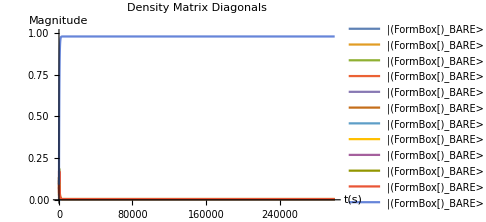
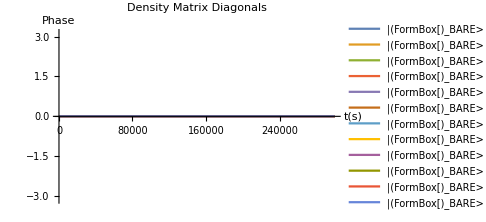

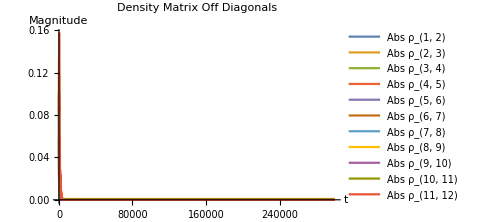
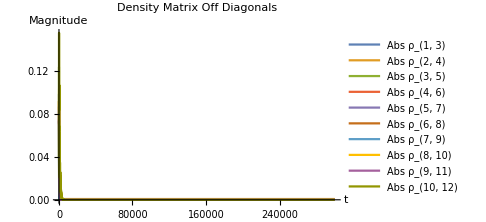
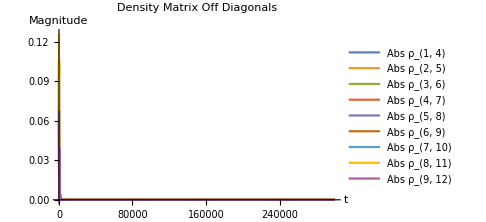

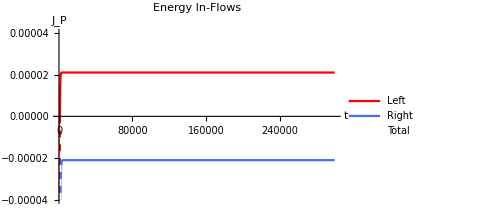

```mathematica
tmax=(150000/Subscript[ω, 2])//.Flatten[{unitassum,Tassum}];

dynamics=NDSolve[
Flatten[{sol//.Flatten[{γassum,NBEassum,unitassum,Tassum,Jassum}],Table[Subscript[ρ, i,j][0]==initρMatrix[[i,j]],{i,1,4Ns},{j,1,4Ns}]}]
,Flatten[Table[Subscript[ρ, i,j],{i,1,4Ns},{j,1,4Ns}]],{t,0,tmax}
];

plot1=Flatten[{Table[Abs[Subscript[ρ, i,i][t]],{i,1,4Ns}]}/.dynamics];
plot2=Flatten[{Table[Arg[Subscript[ρ, i,i][t]],{i,1,4Ns}]}/.dynamics];
{Plot[plot1,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Density Matrix Diagonals"],
	PlotRange-> {0,1},
	AxesLabel->{Style["t(s)"],Style["Magnitude"]}, 
	PlotLegends->Table[StringForm["|(``)_BARE> = |``````>",i,2-EmapL[i],Ns-EmapM[i],2-EmapR[i]],{i,1,4Ns}]
],
Plot[plot2,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Density Matrix Diagonals"],
	PlotRange-> {-π,π},
	AxesLabel->{Style["t(s)"],Style["Phase"]}, 
	PlotLegends->Table[StringForm["|(``)_BARE> = |``````>",i,2-EmapL[i],Ns-EmapM[i],2-EmapR[i]],{i,1,4Ns}]
]}

plot1=Flatten[{Abs[Subscript[ρ, 1,2][t]],Abs[Subscript[ρ, 2,3][t]],Abs[Subscript[ρ, 3,4][t]],Abs[Subscript[ρ, 4,5][t]],Abs[Subscript[ρ, 5,6][t]],Abs[Subscript[ρ, 6,7][t]],Abs[Subscript[ρ, 7,8][t]],Abs[Subscript[ρ, 8,9][t]],Abs[Subscript[ρ, 9,10][t]],Abs[Subscript[ρ, 10,11][t]],Abs[Subscript[ρ, 11,12][t]]}/.dynamics];
plot2=Flatten[{Abs[Subscript[ρ, 1,3][t]],Abs[Subscript[ρ, 2,4][t]],Abs[Subscript[ρ, 3,5][t]],Abs[Subscript[ρ, 4,6][t]],Abs[Subscript[ρ, 5,7][t]],Abs[Subscript[ρ, 6,8][t]],Abs[Subscript[ρ, 7,9][t]],Abs[Subscript[ρ, 8,10][t]],Abs[Subscript[ρ, 9,11][t]],Abs[Subscript[ρ, 10,12][t]]}/.dynamics];
plot3=Flatten[{Abs[Subscript[ρ, 1,4][t]],Abs[Subscript[ρ, 2,5][t]],Abs[Subscript[ρ, 3,6][t]],Abs[Subscript[ρ, 4,7][t]],Abs[Subscript[ρ, 5,8][t]],Abs[Subscript[ρ, 6,9][t]],Abs[Subscript[ρ, 7,10][t]],Abs[Subscript[ρ, 8,11][t]],Abs[Subscript[ρ, 9,12][t]]}/.dynamics];
{
Plot[plot1,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Density Matrix Off Diagonals"],
	PlotRange-> Full,
	AxesLabel->{Style["t"],Style["Magnitude"]}, 
	PlotLegends->{
		Style["Abs ρ_(1, 2)"],Style["Abs ρ_(2, 3)"],
		Style["Abs ρ_(3, 4)"],Style["Abs ρ_(4, 5)"],
		Style["Abs ρ_(5, 6)"],Style["Abs ρ_(6, 7)"],
		Style["Abs ρ_(7, 8)"],Style["Abs ρ_(8, 9)"],
		Style["Abs ρ_(9, 10)"],Style["Abs ρ_(10, 11)"],
		Style["Abs ρ_(11, 12)"]}],
Plot[plot2,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Density Matrix Off Diagonals"],
	PlotRange-> Full,
	AxesLabel->{Style["t"],Style["Magnitude"]}, 
	PlotLegends->{
		Style["Abs ρ_(1, 3)"],Style["Abs ρ_(2, 4)"],
		Style["Abs ρ_(3, 5)"],Style["Abs ρ_(4, 6)"],
		Style["Abs ρ_(5, 7)"],Style["Abs ρ_(6, 8)"],
		Style["Abs ρ_(7, 9)"],Style["Abs ρ_(8, 10)"],
		Style["Abs ρ_(9, 11)"],Style["Abs ρ_(10, 12)"]}],
Plot[plot3,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Density Matrix Off Diagonals"],
	PlotRange-> Full,
	AxesLabel->{Style["t"],Style["Magnitude"]}, 
	PlotLegends->{
		Style["Abs ρ_(1, 4)"],Style["Abs ρ_(2, 5)"],
		Style["Abs ρ_(3, 6)"],Style["Abs ρ_(4, 7)"],
		Style["Abs ρ_(5, 8)"],Style["Abs ρ_(6, 9)"],
		Style["Abs ρ_(7, 10)"],Style["Abs ρ_(8, 11)"],
		Style["Abs ρ_(9, 12)"]}]
}

plot1=Flatten[{Subscript[EngyFlowIn, 1][ρMatrix[t]],Subscript[EngyFlowIn, 2][ρMatrix[t]],Subscript[EngyFlowIn, 1][ρMatrix[t]]+Subscript[EngyFlowIn, 2][ρMatrix[t]]}//.Flatten[{γassum,NBEassum,unitassum,Tassum,Jassum}]/.dynamics];
Plot[plot1,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Energy In-Flows"],
	PlotRange->{-0.00004,0.00004},
	AxesLabel->{"t","J_P"},
	PlotLegends->{"Left ","Right","Total"},
	PlotStyle->{Red,BlueC,{White,Dashed}}]
```

## Partial traces and individual subsystem states

Functions for taking the partial trace for the different subsystems. Here nL, nM, nR are the dimensionalities of the respective subsystems.

```mathematica
PartialTraceL[ρ_,nL_,nM_,nR_]:=Module[{temp0},
Table[Tr[ArrayReshape[Pick[ρ,Table[a,EmapL[i]b,EmapL[j],{i,1,nL nM nR},{j,1,nL nM nR}],1],{(nL nM nR)/nL,(nL nM nR)/nL}]],{a,1,nL},{b,1,nL}]
]
PartialTraceM[ρ_,nL_,nM_,nR_]:=Module[{temp0},
Table[Tr[ArrayReshape[Pick[ρ,Table[a,EmapM[i]b,EmapM[j],{i,1,nL nM nR},{j,1,nL nM nR}],1],{(nL nM nR)/nM,(nL nM nR)/nM}]],{a,1,nM},{b,1,nM}]
]
PartialTraceR[ρ_,nL_,nM_,nR_]:=Module[{temp0},
Table[Tr[ArrayReshape[Pick[ρ,Table[a,EmapR[i]b,EmapR[j],{i,1,nL nM nR},{j,1,nL nM nR}],1],{(nL nM nR)/nR,(nL nM nR)/nR}]],{a,1,nR},{b,1,nR}]
]
```

```mathematica
PartialTraceL[ρMatrix[t],2,Ns,2]//MatrixForm
PartialTraceM[ρMatrix[t],2,Ns,2]//MatrixForm
PartialTraceR[ρMatrix[t],2,Ns,2]//MatrixForm
```

(ρ_(1,1)[t]+ρ_(2,2)[t]+ρ_(3,3)[t]+ρ_(4,4)[t]+ρ_(5,5)[t]+ρ_(6,6)[t] | ρ_(1,7)[t]+ρ_(2,8)[t]+ρ_(3,9)[t]+ρ_(4,10)[t]+ρ_(5,11)[t]+ρ_(6,12)[t]
ρ_(7,1)[t]+ρ_(8,2)[t]+ρ_(9,3)[t]+ρ_(10,4)[t]+ρ_(11,5)[t]+ρ_(12,6)[t] | ρ_(7,7)[t]+ρ_(8,8)[t]+ρ_(9,9)[t]+ρ_(10,10)[t]+ρ_(11,11)[t]+ρ_(12,12)[t])

(ρ_(1,1)[t]+ρ_(2,2)[t]+ρ_(7,7)[t]+ρ_(8,8)[t] | ρ_(1,3)[t]+ρ_(2,4)[t]+ρ_(7,9)[t]+ρ_(8,10)[t] | ρ_(1,5)[t]+ρ_(2,6)[t]+ρ_(7,11)[t]+ρ_(8,12)[t]
ρ_(3,1)[t]+ρ_(4,2)[t]+ρ_(9,7)[t]+ρ_(10,8)[t] | ρ_(3,3)[t]+ρ_(4,4)[t]+ρ_(9,9)[t]+ρ_(10,10)[t] | ρ_(3,5)[t]+ρ_(4,6)[t]+ρ_(9,11)[t]+ρ_(10,12)[t]
ρ_(5,1)[t]+ρ_(6,2)[t]+ρ_(11,7)[t]+ρ_(12,8)[t] | ρ_(5,3)[t]+ρ_(6,4)[t]+ρ_(11,9)[t]+ρ_(12,10)[t] | ρ_(5,5)[t]+ρ_(6,6)[t]+ρ_(11,11)[t]+ρ_(12,12)[t])

(ρ_(1,1)[t]+ρ_(3,3)[t]+ρ_(5,5)[t]+ρ_(7,7)[t]+ρ_(9,9)[t]+ρ_(11,11)[t] | ρ_(1,2)[t]+ρ_(3,4)[t]+ρ_(5,6)[t]+ρ_(7,8)[t]+ρ_(9,10)[t]+ρ_(11,12)[t]
ρ_(2,1)[t]+ρ_(4,3)[t]+ρ_(6,5)[t]+ρ_(8,7)[t]+ρ_(10,9)[t]+ρ_(12,11)[t] | ρ_(2,2)[t]+ρ_(4,4)[t]+ρ_(6,6)[t]+ρ_(8,8)[t]+ρ_(10,10)[t]+ρ_(12,12)[t])

### Dynamics of the complete density matrix

```mathematica
Tassum={Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,Subscript[ω, 1]->1.0 ωconv,Subscript[ω, M]->1.0/p+0.00 ωconv,Subscript[ω, 2]->1.0q/p ωconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.01};
```

```mathematica
γassum={γLM[i_]->0.015ωconv,γMR[i_]->0.015ωconv};
```

```mathematica
tmax=(5000/Subscript[ω, 2])//.Flatten[{unitassum,Tassum}];

dynamics=NDSolve[
Flatten[{sol//.Flatten[{γassum,NBEassum,unitassum,Tassum,Jassum}],Table[Subscript[ρ, i,j][0]==initρMatrix[[i,j]],{i,1,4Ns},{j,1,4Ns}]}]
,Flatten[Table[Subscript[ρ, i,j],{i,1,4Ns},{j,1,4Ns}]],{t,0,tmax}
];

Manipulate[
temp=Abs[ArrayReshape[Table[Subscript[ρ, i,j][t],{i,1,4Ns},{j,1,4Ns}]/.dynamics,{4Ns,4Ns}]];
{ListPointPlot3D[Log[temp],PlotRange->{-15,1},ColorFunction->"TemperatureMap",ImageSize->Large],
DecimalForm[MatrixForm[temp],{4,3}],
MatrixForm[PartialTraceL[temp,2,Ns,2]],
MatrixForm[PartialTraceM[temp,2,Ns,2]],
MatrixForm[PartialTraceR[temp,2,Ns,2]]
}
,{{t,0},0,tmax}]
```

## Numerically obtaining the approximate steady-state

Because ParallelTable doesn’t work properly with EngyFlowIn_P[ρ], we need to redefine them

```mathematica
EngyFlowIn1=Subscript[EngyFlowIn, 1][ρMatrix[t]];
EngyFlowIn2=Subscript[EngyFlowIn, 2][ρMatrix[t]];
```

Basic function for calculating the approximate steady state. This function numerically simulates the system of differential equations for a large time interval, allowing the initial perturbations to die down. The perturbations that do not die down are considered small (see time domain simulation above).

```mathematica
varFunc[T1_,T2_,κ1_,κ2_,ω1_,ωM_,ω2_,γLMs_,γMRs_,tmax_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{unitassum,NBEassum,Jassum,Subscript[T, 1]->T1,Subscript[T, 2]->T2,Subscript[κ, 1]->κ1,Subscript[κ, 2]->κ2,Subscript[ω, 1]->ω1,Subscript[ω, M]->ωM,Subscript[ω, 2]->ω2,Table[γLM[i]->γLMs[[i+1]],{i,0,Ns-1-p}],Table[γMR[i]->γMRs[[i+1]],{i,0,Ns-1-q}]}];
temp1=sol//.temp0;
temp2=NDSolve[
Flatten[{temp1,Table[Subscript[ρ, i,j][0]==i,j i,4Ns 1,{i,1,4Ns},{j,1,4Ns}]}],Flatten[Table[Subscript[ρ, i,j],{i,1,4Ns},{j,1,4Ns}]],{t,0,tmax}];
temp3=Table[Subscript[ρ, i,j][tmax],{i,1,4Ns},{j,1,4Ns}]//.Flatten[temp2];
{
Re[Flatten[Table[Subscript[ρ, i,i][tmax],{i,1,4Ns}]/.temp2]],
Re[Flatten[{EngyFlowIn1,EngyFlowIn2}//.Flatten[{t->tmax,temp0}]/.temp2]]
}
]
```

```mathematica
varFunc[0.2,0.02,0.01,0.01,1.0,1.0/p,1.0q/p,{0.015,0.015,0.015,0.015,0.015},{0.015,0.015,0.015,0.015,0.015,0.015,0.015},50000,unitassum]
```

{{9.82043×10^-8,0.0000221518,0.0000233808,0.0000253518,0.0000214949,0.00452851,0.0000218131,0.00429714,0.00417657,0.00427212,0.00415654,0.978455},{0.0000209997,-0.0000209997}}

At resonant conditions, the steady state definitely exists. Therefore a numerical solution can be obtained by setting time derivatives to zero.

```mathematica
varFunc[T1_,T2_,κ1_,κ2_,ω1_,ωM_,ω2_,γLMs_,γMRs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{unitassum,NBEassum,Jassum,Subscript[T, 1]->T1,Subscript[T, 2]->T2,Subscript[κ, 1]->κ1,Subscript[κ, 2]->κ2,Subscript[ω, 1]->ω1,Subscript[ω, M]->ωM,Subscript[ω, 2]->ω2,Table[γLM[i]->γLMs[[i+1]],{i,0,Ns-1-p}],Table[γMR[i]->γMRs[[i+1]],{i,0,Ns-1-q}]}];
temp1=sol//.temp0;
temp2=NSolve[Flatten[{temp1//.{Subscript[ρ, i_,j_]'[t]->0,Subscript[ρ, i_,j_][t]->Subscript[ρ, i,j]},∑_(i=1)^(4 Ns) Subscript[ρ, i,i]==1}],Flatten[Table[Subscript[ρ, i,j],{i,1,4Ns},{j,1,4Ns}]]];
temp3=Table[Subscript[ρ, i,j],{i,1,4Ns},{j,1,4Ns}]//.Flatten[temp2];
{
Re[Flatten[Table[Subscript[ρ, i,i],{i,1,4Ns}]/.temp2]],
Re[Flatten[{EngyFlowIn1,EngyFlowIn2}//.Flatten[{Subscript[ρ, i_,j_][t]->Subscript[ρ, i,j],temp0}]/.temp2]]
}
]
```

```mathematica
varFunc[0.2,0.02,0.01,0.01,1.0,1.0/p,1.0q/p,{0.015,0.015,0.015,0.015,0.015},{0.015,0.015,0.015,0.015,0.015,0.015,0.015},unitassum]
```

{{9.82043×10^-8,0.0000221518,0.0000233808,0.0000253518,0.0000214949,0.00452851,0.0000218131,0.00429714,0.00417657,0.00427212,0.00415654,0.978455},{0.0000209997,-0.0000209997}}

## Energy flow under different levels of resonance

Energy flows when ω_M is changed from below ω_2 to above ω_2, keeping the γs constant,

```mathematica
PlotEngyFlowsWithω2[T1_,T2_,κ1_,κ2_,ω1s_,ωMmin_,ωMmax_,ω2s_,γLMs_,γMRs_,tmax_,ωres_,legends_,title_]:=Module[{tempx,tempy,temp},
tempx=Table[{ωM,ωM},{ωM,ωMmin,ωMmax,ωres}];
tempy=10^5 ParallelTable[varFunc[T1,T2,κ1,κ2,ω1s,ωM,ω2s,γLMs,γMRs,tmax,unitassum],{ωM,ωMmin,ωMmax,ωres}];
temp=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,2,i]]}],{i,1,2}];
ListPlot[temp,
	PlotRange->{{ωMmin,ωMmax},{-4,4}},
	ImageSize->Medium,
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["ω_H",FontFamily->"Times New Roman",FontSize->16],
		Style["J_P(10^-5)",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	Joined->True,
  PlotLabel->Style[title,FontFamily->"Times New Roman",FontSize->14.5],
	PlotStyle->{{Red},{Blue}},
	PlotLegends->legends &&{
		Style["J_L",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_R",FontFamily->"Times New Roman",FontSize->14.5]}]
]
```

### Effect of increasing high-side jump p, while keeping low-side jump q constant

#### Example case - For N = 3, p = 2 and q = 1

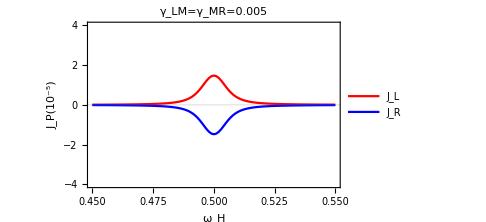
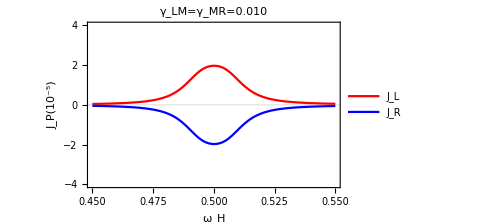
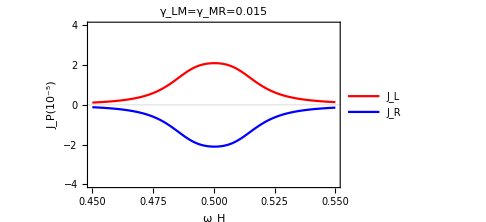

```mathematica
{
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.005ωconv};
γMRs={0.005ωconv,0.005ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.005"]
],
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.01ωconv};
γMRs={0.01ωconv,0.01ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.010"]
],
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.015ωconv};
γMRs={0.015ωconv,0.015ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.015"]
]
}
```

#### Example case - For N = 4, p = 3 and q = 1

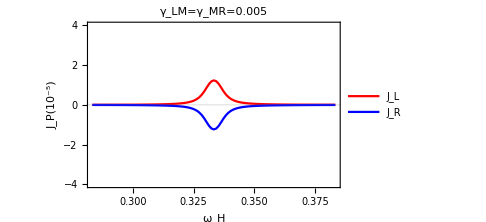
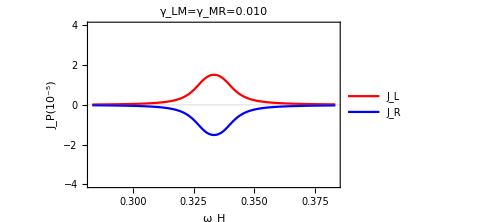
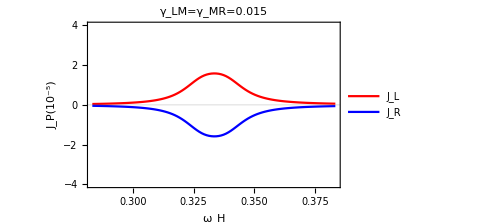

```mathematica
{
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.005ωconv};
γMRs={0.005ωconv,0.005ωconv,0.005ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.005"]
],
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.010ωconv};
γMRs={0.010ωconv,0.010ωconv,0.010ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.010"]
],
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.015ωconv};
γMRs={0.015ωconv,0.015ωconv,0.015ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.015"]
]
}
```

#### Example case - For N = 5, p = 4 and q = 1

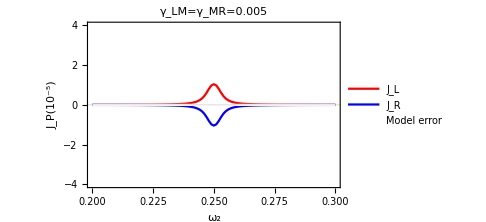
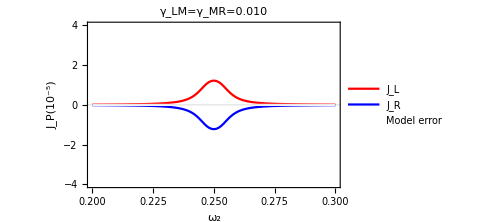
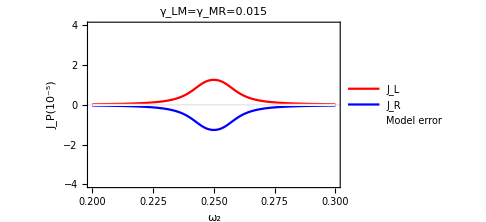

```mathematica
{
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.005ωconv};
γMRs={0.005ωconv,0.005ωconv,0.005ωconv,0.005ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.005"]
],
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.010ωconv};
γMRs={0.010ωconv,0.010ωconv,0.010ωconv,0.010ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.010"]
],
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.015ωconv};
γMRs={0.015ωconv,0.015ωconv,0.015ωconv,0.015ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.015"]
]
}
```

#### Example case - For N = 6, p = 5 and q = 1

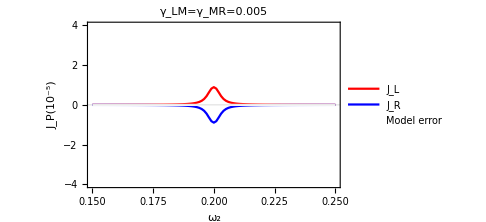
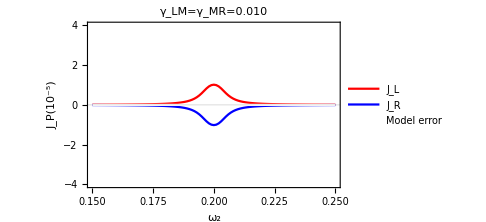
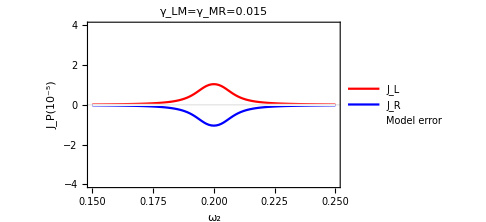

```mathematica
{
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.005ωconv};
γMRs={0.005ωconv,0.005ωconv,0.005ωconv,0.005ωconv,0.005ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.005"]
],
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.010ωconv};
γMRs={0.010ωconv,0.010ωconv,0.010ωconv,0.010ωconv,0.010ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.010"]
],
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.015ωconv};
γMRs={0.015ωconv,0.015ωconv,0.015ωconv,0.015ωconv,0.015ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.015"]
]
}
```

### Effect of increasing number of modelled energy levels N

#### Example case - For N = 3, p = 2 and q = 1

```mathematica
{
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.005ωconv};
γMRs={0.005ωconv,0.005ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.005"]
],
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.01ωconv};
γMRs={0.01ωconv,0.01ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.010"]
],
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.015ωconv};
γMRs={0.015ωconv,0.015ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.015"]
]
}
```

{-Graphics-,-Graphics-,-Graphics-}

#### Example case - For N = 5, p = 2 and q = 1

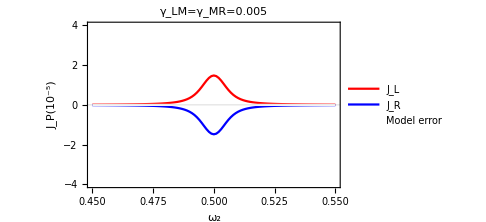
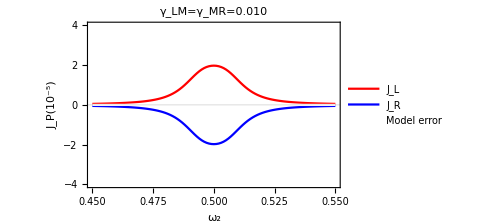
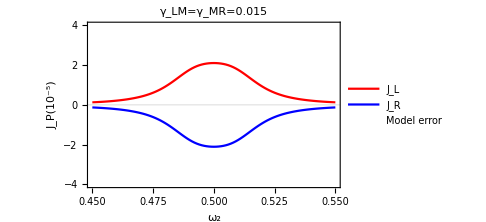

```mathematica
{
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.005ωconv,0.005ωconv,0.005ωconv};
γMRs={0.005ωconv,0.005ωconv,0.005ωconv,0.005ωconv,0.005ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.005"]
],
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.010ωconv,0.010ωconv,0.010ωconv};
γMRs={0.010ωconv,0.010ωconv,0.010ωconv,0.010ωconv,0.010ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.010"]
],
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.015ωconv,0.015ωconv,0.015ωconv};
γMRs={0.015ωconv,0.015ωconv,0.015ωconv,0.015ωconv,0.015ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.015"]
]
}
```

#### Example case - For N = 7, p = 2 and q = 1

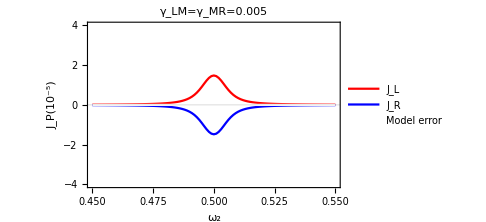
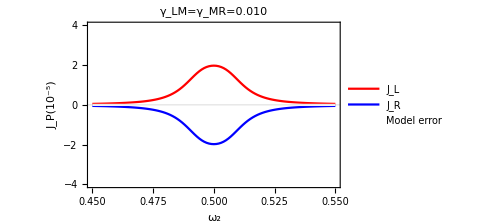
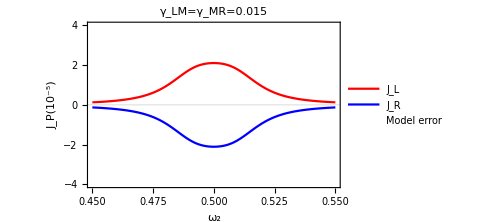

```mathematica
{
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.005ωconv,0.005ωconv,0.005ωconv,0.005ωconv,0.005ωconv};
γMRs={0.005ωconv,0.005ωconv,0.005ωconv,0.005ωconv,0.005ωconv,0.005ωconv,0.005ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.005"]
],
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.010ωconv,0.010ωconv,0.010ωconv,0.010ωconv,0.010ωconv};
γMRs={0.010ωconv,0.010ωconv,0.010ωconv,0.010ωconv,0.010ωconv,0.010ωconv,0.010ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.010"]
],
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.015ωconv,0.015ωconv,0.015ωconv,0.015ωconv,0.015ωconv};
γMRs={0.015ωconv,0.015ωconv,0.015ωconv,0.015ωconv,0.015ωconv,0.015ωconv,0.015ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.015"]
]
}
```

### Badly designed ladder, effectively creating a pumping mechanism

#### Example case - For N = 4, p = 3 and q = 2

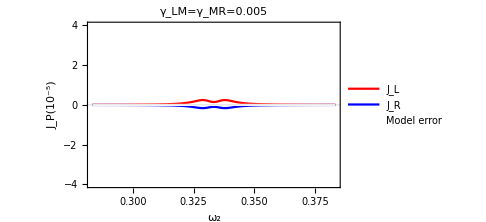
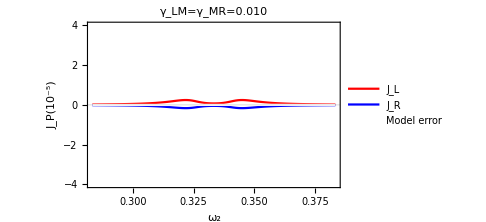
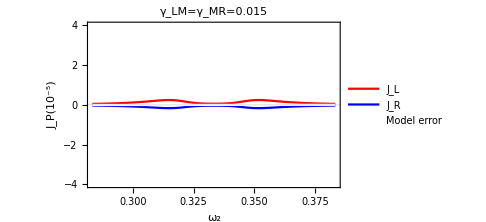

```mathematica
{
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.005ωconv};
γMRs={0.005ωconv,0.005ωconv,0.005ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=150000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.005"]
],
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.010ωconv};
γMRs={0.010ωconv,0.010ωconv,0.010ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=150000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.010"]
],
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.015ωconv};
γMRs={0.015ωconv,0.015ωconv,0.015ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=150000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.015"]
]
}
```

### High order ladder which reduces to a low order system

#### Example case - For N = 5, p = 4 and q = 2

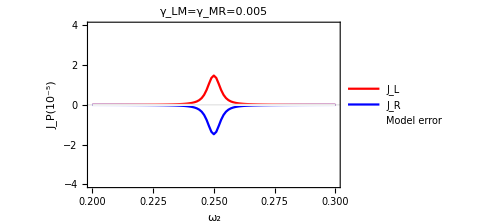
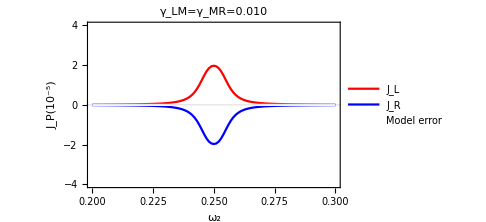
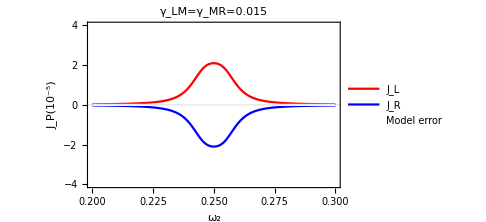

```mathematica
{
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.005ωconv};
γMRs={0.005ωconv,0.005ωconv,0.005ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.005"]
],
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.010ωconv};
γMRs={0.010ωconv,0.010ωconv,0.010ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.010"]
],
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.015ωconv};
γMRs={0.015ωconv,0.015ωconv,0.015ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.015"]
]
}
```

#### which has basically equal behavior to N = 3, p = 2 and q = 1

```mathematica
{
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.005ωconv};
γMRs={0.005ωconv,0.005ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.005"]
],
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.01ωconv};
γMRs={0.01ωconv,0.01ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.010"]
],
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs={0.015ωconv};
γMRs={0.015ωconv,0.015ωconv};
ω1=1.0ωconv;
ωMmin=(1.0/p-0.05)ωconv;ωMmax=(1.0/p+0.05)ωconv;ωres=0.001ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.015"]
]
}
```

{-Graphics-,-Graphics-,-Graphics-}

Note - The apparent doubling of the resonance peak width has no real meaning since the resonance frequency also doubles.

## Energy flow under different levels of resonance and different coupling strengths

We assume all γ terms are equal

```mathematica
PlotEngyFlowsWithω2andγ[T1_,T2_,κ1_,κ2_,ω1s_,ωMmin_,ωMmax_,ω2s_,γmin_,γmax_,tmax_,ωres_,γres_,legends_]:=Module[{tempx,tempy,tempz,temp},
tempx=Table[ωM,{ωM,ωMmin,ωMmax,ωres},{γ,γmin,γmax,γres}];
tempy=Table[γ,{ωM,ωMmin,ωMmax,ωres},{γ,γmin,γmax,γres}];
tempz=10^5 ParallelTable[varFunc[T1,T2,κ1,κ2,ω1s,ωM,ω2s,Table[γ,{i,0,Ns-1-p}],Table[γ,{i,0,Ns-1-q}],tmax,unitassum][[2,1]],{ωM,ωMmin,ωMmax,ωres},{γ,γmin,γmax,γres}];
temp=MapThread[List,{Flatten[tempx][[;;]],Flatten[tempy][[;;]],Flatten[tempz][[;;]]}];
Show[
ListPlot3D[temp,
	PlotRange->{{ωMmin,ωMmax},{γmin,γmax},Full},
	ImageSize->Large,
	AxesStyle->Directive[Darker[Gray],18.5,FontFamily->"Times New Roman"],
	AxesLabel->{
		Style["ω_H/Δ",FontFamily->"Times New Roman",FontSize->19.5],
		Style["γ/Δ",FontFamily->"Times New Roman",FontSize->19.5]},
	ColorFunction->"BlueGreenYellow"],
Graphics3D[Text[Style["10^-5J_L/ℏΔ^2",Darker[Gray],FontFamily->"Times New Roman",FontSize->19.5],Scaled[{0.135,0.03,0.73}]]]
]
]
```

### Effect of increasing high-side jump p, while keeping low-side jump q constant

#### Example case - For N = 3, p = 2 and q = 1

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γmin,γmax,tmaxs,ωres,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.00ωconv;γmax=0.015 ωconv;γres=0.00075;
ω1=1.0ωconv;
ωMmin=(0.9/p)ωconv;ωMmax=(1.1/p)ωconv;ωres=((1.1-0.9)/(50p))ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2andγ[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γmin,γmax,tmaxs,ωres,γres,True]
]//AbsoluteTiming
```

{131.878,-Graphics3D-}

#### Example case - For N = 4, p = 3 and q = 1

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γmin,γmax,tmaxs,ωres,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.00ωconv;γmax=0.015 ωconv;γres=0.00075;
ω1=1.0ωconv;
ωMmin=(0.9/p)ωconv;ωMmax=(1.1/p)ωconv;ωres=((1.1-0.9)/(50p))ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2andγ[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γmin,γmax,tmaxs,ωres,γres,True]
]//AbsoluteTiming
```

{221.125,-Graphics3D-}

#### Example case - For N = 5, p = 4 and q = 1

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γmin,γmax,tmaxs,ωres,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.00ωconv;γmax=0.015 ωconv;γres=0.00075;
ω1=1.0ωconv;
ωMmin=(0.9/p)ωconv;ωMmax=(1.1/p)ωconv;ωres=((1.1-0.9)/(50p))ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2andγ[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γmin,γmax,tmaxs,ωres,γres,True]
]//AbsoluteTiming
```

{339.671,-Graphics3D-}

#### Example case - For N = 6, p = 5 and q = 1

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γmin,γmax,tmaxs,ωres,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.00ωconv;γmax=0.015 ωconv;γres=0.00075;
ω1=1.0ωconv;
ωMmin=(0.9/p)ωconv;ωMmax=(1.1/p)ωconv;ωres=((1.1-0.9)/(50p))ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2andγ[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γmin,γmax,tmaxs,ωres,γres,True]
]//AbsoluteTiming
```

{464.252,-Graphics3D-}

### Effect of increasing number of modelled energy levels N

#### Example case - For N = 3, p = 2 and q = 1

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γmin,γmax,tmaxs,ωres,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.00ωconv;γmax=0.015 ωconv;γres=0.00075;
ω1=1.0ωconv;
ωMmin=(0.9/p)ωconv;ωMmax=(1.1/p)ωconv;ωres=((1.1-0.9)/(50p))ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2andγ[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γmin,γmax,tmaxs,ωres,γres,True]
]//AbsoluteTiming
```

{132.594,-Graphics3D-}

#### Example case - For N = 5, p = 2 and q = 1

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γmin,γmax,tmaxs,ωres,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.00ωconv;γmax=0.015 ωconv;γres=0.00075;
ω1=1.0ωconv;
ωMmin=(0.9/p)ωconv;ωMmax=(1.1/p)ωconv;ωres=((1.1-0.9)/(50p))ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2andγ[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γmin,γmax,tmaxs,ωres,γres,True]
]//AbsoluteTiming
```

{373.584,-Graphics3D-}

#### Example case - For N = 7, p = 2 and q = 1

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γmin,γmax,tmaxs,ωres,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.00ωconv;γmax=0.015 ωconv;γres=0.00075;
ω1=1.0ωconv;
ωMmin=(0.9/p)ωconv;ωMmax=(1.1/p)ωconv;ωres=((1.1-0.9)/(50p))ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2andγ[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γmin,γmax,tmaxs,ωres,γres,True]
]//AbsoluteTiming
```

{701.015,-Graphics3D-}

### Badly designed ladder, effectively creating a pumping mechanism

#### Example case - For N = 4, p = 3 and q = 2

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γmin,γmax,tmaxs,ωres,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.00ωconv;γmax=0.015 ωconv;γres=0.00075;
ω1=1.0ωconv;
ωMmin=(0.9/p)ωconv;ωMmax=(1.1/p)ωconv;ωres=((1.1-0.9)/(50p))ωconv;
ω2=1.0q/p ωconv;
tmaxs=300000/ωconv;
PlotEngyFlowsWithω2andγ[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γmin,γmax,tmaxs,ωres,γres,True]
]//AbsoluteTiming
```

{1327.32,-Graphics3D-}

Note - The thermal flows at this point are simply from the density matrix not being stationary yet at the end of the time-domain simulation. At infinitely long times, the flows would be always zero.

### High order ladder which reduces to a low order system

#### Example case - For N = 5, p = 4 and q = 2

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γmin,γmax,tmaxs,ωres,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.00ωconv;γmax=0.015 ωconv;γres=0.00150;
ω1=1.0ωconv;
ωMmin=(0.9/p)ωconv;ωMmax=(1.1/p)ωconv;ωres=((1.1-0.9)/(50p))ωconv;
ω2=1.0q/p ωconv;
tmaxs=150000/ωconv;
PlotEngyFlowsWithω2andγ[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γmin,γmax,tmaxs,ωres,γres,True]
]//AbsoluteTiming
```

{484.346,-Graphics3D-}

#### which has basically equal behavior to N = 3, p = 2 and q = 1

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γmin,γmax,tmaxs,ωres,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.00ωconv;γmax=0.015 ωconv;γres=0.00075;
ω1=1.0ωconv;
ωMmin=(0.9/p)ωconv;ωMmax=(1.1/p)ωconv;ωres=((1.1-0.9)/(50p))ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2andγ[T1,T2,κ1,κ2,ω1,ωMmin,ωMmax,ω2,γmin,γmax,tmaxs,ωres,γres,True]
]//AbsoluteTiming
```

{132.506,-Graphics3D-}

## Energy flow under intermediate bath formalism

Data taken from “Two TLS connected to thermal baths each - Intermediate bath coupling.m”

We study the following case,
	1. Hot left reservoir at T_1 = 0.2
	2. Cold right reservoir at T_2 = 0.02
	3. Two TLS and an intermediate bath with unknown temperature T_I in between
	4. All bath couplings are weak at κ = 0.01
	5. Left TLS has ω = 1.0
	6. Right TLS has ω = 1.0q/p
Intermediate bath formalism utilized to calculate T_I

Steady state energy flow of a single TLS connected to two thermal baths of different temperatures,

```mathematica
OneTLSEnergyFlow[ω_,T1_,T2_,κ1_,κ2_]:=-((ⅇ^(ω/T1)-ⅇ^(ω/T2)) κ1 κ2 ω^2)/((ⅇ^(ω/T1)+1) (ⅇ^(ω/T2)-1) κ1+(ⅇ^(ω/T1)-1) (ⅇ^(ω/T2)+1) κ2)
```

We find the steady state by calculating the temperature T_I; where the input thermal flow J_L from left bath to TLS L, equals the input thermal flow J_I from intermediate bath I to TLS R.

#### Example case - For N = 3, p = 2 and q = 1

```mathematica
Ns=3;p=2;q=1;
EL=OneTLSEnergyFlow[1.0ωconv,0.2 Tconv,TI,0.01,0.01];
EI=OneTLSEnergyFlow[1.0q/p ωconv,TI,0.02 Tconv,0.01,0.01];

TIstat = TI/.FindRoot[EL-EI,{TI,0.02}];
ELstat = EL/.TI->TIstat
```

0.0000306782

#### Example case - For N = 4, p = 3 and q = 1

```mathematica
Ns=4;p=3;q=1;
EL=OneTLSEnergyFlow[1.0ωconv,0.2 Tconv,TI,0.01,0.01];
EI=OneTLSEnergyFlow[1.0q/p ωconv,TI,0.02 Tconv,0.01,0.01];

TIstat = TI/.FindRoot[EL-EI,{TI,0.02}];
ELstat = EL/.TI->TIstat
```

0.0000326727

#### Example case - For N = 5, p = 4 and q = 1

```mathematica
Ns=5;p=4;q=1;
EL=OneTLSEnergyFlow[1.0ωconv,0.2 Tconv,TI,0.01,0.01];
EI=OneTLSEnergyFlow[1.0q/p ωconv,TI,0.02 Tconv,0.01,0.01];

TIstat = TI/.FindRoot[EL-EI,{TI,0.02}];
ELstat = EL/.TI->TIstat
```

0.0000330631

#### Example case - For N = 6, p = 5 and q = 1

```mathematica
Ns=6;p=5;q=1;
EL=OneTLSEnergyFlow[1.0ωconv,0.2 Tconv,TI,0.01,0.01];
EI=OneTLSEnergyFlow[1.0q/p ωconv,TI,0.02 Tconv,0.01,0.01];

TIstat = TI/.FindRoot[EL-EI,{TI,0.02}];
ELstat = EL/.TI->TIstat
```

0.0000330709

#### Example case - For N = 4, p = 3 and q = 2

```mathematica
Ns=4;p=3;q=2;
EL=OneTLSEnergyFlow[1.0ωconv,0.2 Tconv,TI,0.01,0.01];
EI=OneTLSEnergyFlow[1.0q/p ωconv,TI,0.02 Tconv,0.01,0.01];

TIstat = TI/.FindRoot[EL-EI,{TI,0.02}];
ELstat = EL/.TI->TIstat
```

0.0000269954

#### Example case - For N = 5, p = 4 and q = 2

```mathematica
Ns=5;p=4;q=2;
EL=OneTLSEnergyFlow[1.0ωconv,0.2 Tconv,TI,0.01,0.01];
EI=OneTLSEnergyFlow[1.0q/p ωconv,TI,0.02 Tconv,0.01,0.01];

TIstat = TI/.FindRoot[EL-EI,{TI,0.02}];
ELstat = EL/.TI->TIstat
```

0.0000306782

## Effect of interaction strengths on the thermal flows at resonance

### Change both high-side (γ_LM) and low-side (γ_MR) interaction strengths

Plot the effect of the coupling strengths γ_LM and γ_MR on the energy flows at resonance

```mathematica
PlotEngyFlowsWithγ[T1_,T2_,κ1_,κ2_,ω1s_,ωMs_,ω2s_,γmin_,γmax_,γres_,legends_]:=Module[{tempx,tempy,tempz,temp},
tempx=Table[γLM,{γLM,γmin,γmax,γres},{γMR,γmin,γmax,γres}];
tempy=Table[γMR,{γLM,γmin,γmax,γres},{γMR,γmin,γmax,γres}];
tempz=10^5 ParallelTable[varFunc[T1,T2,κ1,κ2,ω1s,ωMs,ω2s,Table[γLM,{i,0,Ns-1-p}],Table[γMR,{i,0,Ns-1-q}],unitassum][[2,1]],{γLM,γmin,γmax,γres},{γMR,γmin,γmax,γres}];
temp=MapThread[List,{Flatten[tempx][[;;]],Flatten[tempy][[;;]],Flatten[tempz][[;;]]}];
Show[
ListPlot3D[temp,
	PlotRange->{{γmin,γmax},{γmin,γmax},Full},
	ImageSize->Large,
	AxesStyle->Directive[Darker[Gray],18.5,FontFamily->"Times New Roman"],
	AxesLabel->{
		Style["γ_H1",FontFamily->"Times New Roman",FontSize->19.5],
		Style["γ_H2",FontFamily->"Times New Roman",FontSize->19.5]},
	ColorFunction->"BlueGreenYellow"],
Graphics3D[Text[Style["10^-5J_L/ℏΔ^2",Darker[Gray],FontFamily->"Times New Roman",FontSize->19.5],Scaled[{0.135,0.03,0.93}]]]
]
]
```

Non-resonant numerical simulation, just to check that previous results are correct

```mathematica
PlotEngyFlowsWithγ[T1_,T2_,κ1_,κ2_,ω1s_,ωMs_,ω2s_,γmin_,γmax_,tmax_,γres_,legends_]:=Module[{tempx,tempy,tempz,temp},
tempx=Table[γLM,{γLM,γmin,γmax,γres},{γMR,γmin,γmax,γres}];
tempy=Table[γMR,{γLM,γmin,γmax,γres},{γMR,γmin,γmax,γres}];
tempz=10^5 ParallelTable[varFunc[T1,T2,κ1,κ2,ω1s,ωMs,ω2s,Table[γLM,{i,0,Ns-1-p}],Table[γMR,{i,0,Ns-1-q}],tmax,unitassum][[2,1]],{γLM,γmin,γmax,γres},{γMR,γmin,γmax,γres}];
temp=MapThread[List,{Flatten[tempx][[;;]],Flatten[tempy][[;;]],Flatten[tempz][[;;]]}];
Show[
ListPlot3D[temp,
	PlotRange->{{γmin,γmax},{γmin,γmax},Full},
	ImageSize->Large,
	AxesStyle->Directive[Darker[Gray],18.5,FontFamily->"Times New Roman"],
	AxesLabel->{
		Style["γ_H1",FontFamily->"Times New Roman",FontSize->19.5],
		Style["γ_H2",FontFamily->"Times New Roman",FontSize->19.5]},
	ColorFunction->"BlueGreenYellow"],
Graphics3D[Text[Style["10^-5J_L/ℏΔ^2",Darker[Gray],FontFamily->"Times New Roman",FontSize->19.5],Scaled[{0.135,0.03,0.93}]]]
]
]
```

#### Example case - For N = 3, p = 2 and q = 1

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,tmaxs,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.0005ωconv;γmax=0.03 ωconv;γres=0.0005ωconv;
ω1=1.0ωconv;
ωM=(1.0/p)ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithγ[T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,tmaxs,γres,True]
]//AbsoluteTiming
```

{48.7855,-Graphics3D-}

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.0005ωconv;γmax=0.03 ωconv;γres=0.0005ωconv;
ω1=1.0ωconv;
ωM=(1.0/p)ωconv;
ω2=1.0q/p ωconv;
PlotEngyFlowsWithγ[T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,γres,True]
]//AbsoluteTiming
```

{26.7593,-Graphics3D-}

#### Example case - For N = 4, p = 3 and q = 1

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,tmaxs,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.0005ωconv;γmax=0.03 ωconv;γres=0.0005ωconv;
ω1=1.0ωconv;
ωM=(1.0/p)ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithγ[T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,tmaxs,γres,True]
]//AbsoluteTiming
```

{107.972,-Graphics3D-}

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.0005ωconv;γmax=0.03 ωconv;γres=0.0005;
ω1=1.0ωconv;
ωM=(1.0/p)ωconv;
ω2=1.0q/p ωconv;
PlotEngyFlowsWithγ[T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,γres,True]
]//AbsoluteTiming
```

{32.21,-Graphics3D-}

#### Example case - For N = 5, p = 4 and q = 1

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,tmaxs,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.0005ωconv;γmax=0.03 ωconv;γres=0.0005ωconv;
ω1=1.0ωconv;
ωM=(1.0/p)ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithγ[T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,tmaxs,γres,True]
]//AbsoluteTiming
```

{78.3772,-Graphics3D-}

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.0005ωconv;γmax=0.03 ωconv;γres=0.0005ωconv;
ω1=1.0ωconv;
ωM=(1.0/p)ωconv;
ω2=1.0q/p ωconv;
PlotEngyFlowsWithγ[T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,γres,True]
]//AbsoluteTiming
```

{15.4541,-Graphics3D-}

#### Example case - For N = 6, p = 5 and q = 1

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,tmaxs,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.0005ωconv;γmax=0.03 ωconv;γres=0.0005ωconv;
ω1=1.0ωconv;
ωM=(1.0/p)ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithγ[T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,tmaxs,γres,True]
]//AbsoluteTiming
```

{133.268,-Graphics3D-}

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.0005ωconv;γmax=0.03 ωconv;γres=0.0005ωconv;
ω1=1.0ωconv;
ωM=(1.0/p)ωconv;
ω2=1.0q/p ωconv;
PlotEngyFlowsWithγ[T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,γres,True]
]//AbsoluteTiming
```

{23.3592,-Graphics3D-}

#### Example case - For N = 5, p = 2 and q = 1

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,tmaxs,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.0005ωconv;γmax=0.03 ωconv;γres=0.0005ωconv;
ω1=1.0ωconv;
ωM=(1.0/p)ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithγ[T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,tmaxs,γres,True]
]//AbsoluteTiming
```

{73.9699,-Graphics3D-}

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.0005ωconv;γmax=0.03 ωconv;γres=0.0005ωconv;
ω1=1.0ωconv;
ωM=(1.0/p)ωconv;
ω2=1.0q/p ωconv;
PlotEngyFlowsWithγ[T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,γres,True]
]//AbsoluteTiming
```

{18.3274,-Graphics3D-}

#### Example case - For N = 7, p = 2 and q = 1

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,tmaxs,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.0005ωconv;γmax=0.03 ωconv;γres=0.0005ωconv;
ω1=1.0ωconv;
ωM=(1.0/p)ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithγ[T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,tmaxs,γres,True]
]//AbsoluteTiming
```

{182.108,-Graphics3D-}

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.0005ωconv;γmax=0.03 ωconv;γres=0.0005ωconv;
ω1=1.0ωconv;
ωM=(1.0/p)ωconv;
ω2=1.0q/p ωconv;
PlotEngyFlowsWithγ[T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,γres,True]
]//AbsoluteTiming
```

{42.6422,-Graphics3D-}

#### Example case - For N = 4, p = 3 and q = 2

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,tmaxs,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.0005ωconv;γmax=0.03 ωconv;γres=0.0005ωconv;
ω1=1.0ωconv;
ωM=(1.0/p)ωconv;
ω2=1.0q/p ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithγ[T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,tmaxs,γres,True]
]//AbsoluteTiming
```

{29.0665,-Graphics3D-}

Note - The above values come only because the stationary state is not reached within the time-domain simulation interval. Below is the more correct simulation.

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.0005ωconv;γmax=0.03 ωconv;γres=0.0005ωconv;
ω1=1.0ωconv;
ωM=(1.0/p)ωconv;
ω2=1.0q/p ωconv;
PlotEngyFlowsWithγ[T1,T2,κ1,κ2,ω1,ωM,ω2,γmin,γmax,γres,True]
]//AbsoluteTiming
```

{9.20185,-Graphics3D-}

### For the case N = 3, p = 2, q = 1, change the ratio of low-side (γ_MR) interaction strengths, keeping high-side (γ_LM) constant

```mathematica
PlotEngyFlowsWithγMR[T1_,T2_,κ1_,κ2_,ω1s_,ωHs_,ω2s_,γLMs_,γmin_,γmax_,γres_,legends_]:=Module[{tempx,tempy,tempz,temp},
tempx=Table[γMR0,{γMR0,γmin,γmax,γres},{γMR1,γmin,γmax,γres}];
tempy=Table[γMR1,{γMR0,γmin,γmax,γres},{γMR1,γmin,γmax,γres}];
tempz=10^5 ParallelTable[varFunc[T1,T2,κ1,κ2,ω1s,ωHs,ω2s,{γLMs},{γMR0,γMR1},unitassum][[2,1]],{γMR0,γmin,γmax,γres},{γMR1,γmin,γmax,γres}];
temp=MapThread[List,{Flatten[tempx][[;;]],Flatten[tempy][[;;]],Flatten[tempz][[;;]]}];
Show[
ListPlot3D[temp,
	PlotRange->{{γmin,γmax},{γmin,γmax},Full},
	ImageSize->Large,
	AxesStyle->Directive[Darker[Gray],18.5,FontFamily->"Times New Roman"],
	AxesLabel->{
		Style["γ_H2(0)",FontFamily->"Times New Roman",FontSize->19.5],
		Style["γ_H2(1)",FontFamily->"Times New Roman",FontSize->19.5]},
	ColorFunction->"BlueGreenYellow"],
Graphics3D[Text[Style["10^-5J_L/ℏΔ^2",Darker[Gray],FontFamily->"Times New Roman",FontSize->19.5],Scaled[{0.135,0.03,0.93}]]]
]
]
```

Non-resonant numerical simulation, just to check that previous results are correct

```mathematica
PlotEngyFlowsWithγMR[T1_,T2_,κ1_,κ2_,ω1s_,ωHs_,ω2s_,γLMs_,γmin_,γmax_,tmax_,γres_,legends_]:=Module[{tempx,tempy,tempz,temp},
tempx=Table[γMR0,{γMR0,γmin,γmax,γres},{γMR1,γmin,γmax,γres}];
tempy=Table[γMR1,{γMR0,γmin,γmax,γres},{γMR1,γmin,γmax,γres}];
tempz=10^5 ParallelTable[varFunc[T1,T2,κ1,κ2,ω1s,ωHs,ω2s,{γLMs},{γMR0,γMR1},tmax,unitassum][[2,1]],{γMR0,γmin,γmax,γres},{γMR1,γmin,γmax,γres}];
temp=MapThread[List,{Flatten[tempx][[;;]],Flatten[tempy][[;;]],Flatten[tempz][[;;]]}];
Show[
ListPlot3D[temp,
	PlotRange->{{γmin,γmax},{γmin,γmax},Full},
	ImageSize->Large,
	AxesStyle->Directive[Darker[Gray],18.5,FontFamily->"Times New Roman"],
	AxesLabel->{
		Style["γ_H2(0)",FontFamily->"Times New Roman",FontSize->19.5],
		Style["γ_H2(1)",FontFamily->"Times New Roman",FontSize->19.5]},
	ColorFunction->"BlueGreenYellow"],
Graphics3D[Text[Style["10^-5J_L/ℏΔ^2",Darker[Gray],FontFamily->"Times New Roman",FontSize->19.5],Scaled[{0.135,0.03,0.93}]]]
]
]
```

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ω2,ω3,γLM,γmin,γmax,tmaxs,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.00ωconv;γmax=0.04 ωconv;γres=0.0010;
ω1=1.0ωconv;
ω2=(1.0/p)ωconv;
ω3=1.0q/p ωconv;
γLM=0.020ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithγMR[T1,T2,κ1,κ2,ω1,ω2,ω3,γLM,γmin,γmax,tmaxs,γres,True]
]//AbsoluteTiming
```

{26.4289,-Graphics3D-}

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ω2,ω3,γLM,γmin,γmax,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.00ωconv;γmax=0.04 ωconv;γres=0.0010;
ω1=1.0ωconv;
ω2=(1.0/p)ωconv;
ω3=1.0q/p ωconv;
γLM=0.020ωconv;
PlotEngyFlowsWithγMR[T1,T2,κ1,κ2,ω1,ω2,ω3,γLM,γmin,γmax,γres,True]
]//AbsoluteTiming
```

{13.79,-Graphics3D-}

### For the case N = 4, p = 3, q = 1, change the ratio of low-side interaction strengths, keeping high-side constant

```mathematica
PlotEngyFlowsWithγMR[T1_,T2_,κ1_,κ2_,ω1s_,ωMs_,ω2s_,γLMs_,γMR1min_,γMR1max_,γMR1res_,γMR2min_,γMR2max_,γMR2res_,legends_]:=Module[{tempx,tempy,tempz,temp},
tempx=Table[γMR1,{γMR1,γMR1min,γMR1max,γMR1res},{γMR2,γMR2min,γMR2max,γMR2res}];
tempy=Table[γMR2,{γMR1,γMR1min,γMR1max,γMR1res},{γMR2,γMR2min,γMR2max,γMR2res}];
tempz=10^5 ParallelTable[varFunc[T1,T2,κ1,κ2,ω1s,ωMs,ω2s,{γLMs},{γLMs,γMR1,γMR2},unitassum][[2,1]],{γMR1,γMR1min,γMR1max,γMR1res},{γMR2,γMR2min,γMR2max,γMR2res}];
temp=MapThread[List,{Flatten[tempx][[;;]],Flatten[tempy][[;;]],Flatten[tempz][[;;]]}];
Show[
ListPlot3D[temp,
	PlotRange->{{γMR1min,γMR1max},{γMR2min,γMR2max},Full},
	ImageSize->Large,
	AxesStyle->Directive[Darker[Gray],18.5,FontFamily->"Times New Roman"],
	AxesLabel->{
		Style["γ_H2(1)",FontFamily->"Times New Roman",FontSize->19.5],
		Style["γ_H2(2)",FontFamily->"Times New Roman",FontSize->19.5]},
	ColorFunction->"BlueGreenYellow"],
Graphics3D[Text[Style["10^-5J_L/ℏΔ^2",Darker[Gray],FontFamily->"Times New Roman",FontSize->19.5],Scaled[{0.135,0.03,0.73}]]]
]
]
```

Non-resonant numerical simulation, just to check that previous results are correct

```mathematica
PlotEngyFlowsWithγMR[T1_,T2_,κ1_,κ2_,ω1s_,ωMs_,ω2s_,γLMs_,γMR1min_,γMR1max_,γMR1res_,γMR2min_,γMR2max_,γMR2res_,tmax_,legends_]:=Module[{tempx,tempy,tempz,temp},
tempx=Table[γMR1,{γMR1,γMR1min,γMR1max,γMR1res},{γMR2,γMR2min,γMR2max,γMR2res}];
tempy=Table[γMR2,{γMR1,γMR1min,γMR1max,γMR1res},{γMR2,γMR2min,γMR2max,γMR2res}];
tempz=10^5 ParallelTable[varFunc[T1,T2,κ1,κ2,ω1s,ωMs,ω2s,{γLMs},{γLMs,γMR1,γMR2},tmax,unitassum][[2,1]],{γMR1,γMR1min,γMR1max,γMR1res},{γMR2,γMR2min,γMR2max,γMR2res}];
temp=MapThread[List,{Flatten[tempx][[;;]],Flatten[tempy][[;;]],Flatten[tempz][[;;]]}];
Show[
ListPlot3D[temp,
	PlotRange->{{γMR1min,γMR1max},{γMR2min,γMR2max},Full},
	ImageSize->Large,
	AxesStyle->Directive[Darker[Gray],18.5,FontFamily->"Times New Roman"],
	AxesLabel->{
		Style["γ_H2(1)",FontFamily->"Times New Roman",FontSize->19.5],
		Style["γ_H2(2)",FontFamily->"Times New Roman",FontSize->19.5]},
	ColorFunction->"BlueGreenYellow"],
Graphics3D[Text[Style["10^-5J_L/ℏΔ^2",Darker[Gray],FontFamily->"Times New Roman",FontSize->19.5],Scaled[{0.135,0.03,0.73}]]]
]
]
```

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ω2,ω3,γLM,γMR1min,γMR1max,γMR1res,γMR2min,γMR2max,γMR2res,tmaxs},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γMR1min=0.00ωconv;γMR1max=0.005 ωconv;γMR1res=0.00005;
γMR2min=0.00ωconv;γMR2max=0.025 ωconv;γMR2res=0.00025;
ω1=1.0ωconv;
ω2=(1.0/p)ωconv;
ω3=1.0q/p ωconv;
γLM=0.015ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithγMR[T1,T2,κ1,κ2,ω1,ω2,ω3,γLM,γMR1min,γMR1max,γMR1res,γMR2min,γMR2max,γMR2res,tmaxs,True]
]//AbsoluteTiming
```

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ω2,ω3,γLM,γMR1min,γMR1max,γMR1res,γMR2min,γMR2max,γMR2res},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γMR1min=0.00ωconv;γMR1max=0.005 ωconv;γMR1res=0.00005;
γMR2min=0.00ωconv;γMR2max=0.025 ωconv;γMR2res=0.00025;
ω1=1.0ωconv;
ω2=(1.0/p)ωconv;
ω3=1.0q/p ωconv;
γLM=0.015ωconv;
PlotEngyFlowsWithγMR[T1,T2,κ1,κ2,ω1,ω2,ω3,γLM,γMR1min,γMR1max,γMR1res,γMR2min,γMR2max,γMR2res,True]
]//AbsoluteTiming
```

{89.2022,-Graphics3D-}

## Under resonant conditions - compare the energy divider mechanism with intermediate bath mechanism

```mathematica
OneTLSEnergyFlow[ω_,T1_,T2_,κ1_,κ2_]:=-((ⅇ^(ω/T1)-ⅇ^(ω/T2)) κ1 κ2 ω^2)/((ⅇ^(ω/T1)+1) (ⅇ^(ω/T2)-1) κ1+(ⅇ^(ω/T1)-1) (ⅇ^(ω/T2)+1) κ2)
```

We vary the temperatures on both sides,
	observe the thermal flow through energy divider mechanism

```mathematica
PlotEngyFlowsWithT[T1min_,T1max_,T1res_,T2min_,T2max_,T2res_,κ1_,κ2_,ω1s_,ωMs_,ω2s_,γs_,legends_]:=Module[{tempx,tempy,tempz,temp},
tempx=Table[T1,{T1,T1min,T1max,T1res},{T2,T2min,T2max,T2res}];
tempy=Table[T2,{T1,T1min,T1max,T1res},{T2,T2min,T2max,T2res}];
tempz=10^5 ParallelTable[varFunc[T1,T2,κ1,κ2,ω1s,ωMs,ω2s,Table[γs,{i,0,Ns-1-p}],Table[γs,{i,0,Ns-1-q}],unitassum][[2,1]],{T1,T1min,T1max,T1res},{T2,T2min,T2max,T2res}];
temp=MapThread[List,{Flatten[tempx][[;;]],Flatten[tempy][[;;]],Flatten[Abs[tempz]][[;;]]}];
Show[
ListPlot3D[temp,
	PlotRange->{{T1min,T1max},{T2min,T2max},Full},
	ImageSize->Large,
	AxesStyle->Directive[Darker[Gray],18.5,FontFamily->"Times New Roman"],
	AxesLabel->{
		Style["k_BT_1/ℏΔ",FontFamily->"Times New Roman",FontSize->19.5],
		Style["k_BT_2/ℏΔ",FontFamily->"Times New Roman",FontSize->19.5]},
	ColorFunction->"BlueGreenYellow"],
Graphics3D[Text[Style["10^-5J_L/ℏΔ^2",Darker[Gray],FontFamily->"Times New Roman",FontSize->19.5],Scaled[{0.135,0.03,0.73}]]]
]
]
```

observe the thermal flow through intermediate bath mechanism

```mathematica
PlotIntEngyFlowsWithT[T1min_,T1max_,T1res_,T2min_,T2max_,T2res_,κ1_,κ2_,κI_,ω1s_,ω2s_,title_]:=
Module[{tempx,tempy,tempz,temp},
tempx=Table[T1,{T1,T1min,T1max,T1res},{T2,T2min,T2max,T2res}];
tempy=Table[T2,{T1,T1min,T1max,T1res},{T2,T2min,T2max,T2res}];
tempz=10^5 Table[OneTLSEnergyFlow[ω1s,T1,TI,κ1,κI]/.(FindRoot[OneTLSEnergyFlow[ω1s,T1,TI,κ1,κI]-OneTLSEnergyFlow[ω2s,TI,T2,κI,κ2],{TI,T1min}]),{T1,T1min,T1max,T1res},{T2,T2min,T2max,T2res}];
temp=MapThread[List,{Flatten[tempx][[;;]],Flatten[tempy][[;;]],Flatten[Abs[tempz]][[;;]]}];
Show[
ListPlot3D[temp,
	PlotRange->{{T1min,T1max},{T2min,T2max},Full},
	ImageSize->Large,
	AxesStyle->Directive[Darker[Gray],18.5,FontFamily->"Times New Roman"],
	AxesLabel->{
		Style["k_BT_1/ℏΔ",FontFamily->"Times New Roman",FontSize->19.5],
		Style["k_BT_2/ℏΔ",FontFamily->"Times New Roman",FontSize->19.5]},
	ColorFunction->"BlueGreenYellow"],
Graphics3D[Text[Style["10^-5J_L/ℏΔ^2",Darker[Gray],FontFamily->"Times New Roman",FontSize->19.5],Scaled[{0.135,0.03,0.73}]]]
]
]
```

#### Example case - For N = 3, p = 2 and q = 1, with intermediate bath κ, equal to the external bath κs or κ maximal

```mathematica
{Module[{T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,ω1,ωM,ω2,γ},
T1min=0.02Tconv;T1max=0.5Tconv;T1res=0.02Tconv;
T2min=0.02Tconv;T2max=0.5Tconv;T2res=0.02Tconv;
κ1=0.01;κ2=0.01;
γ=0.015ωconv;
ω1=1.0ωconv;
ωM=1.0/p ωconv;
ω2=1.0q/p ωconv;
PlotEngyFlowsWithT[T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,ω1,ωM,ω2,γ,True]
],
Module[{T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2},
T1min=0.02Tconv;T1max=0.5Tconv;T1res=0.02Tconv;
T2min=0.02Tconv;T2max=0.5Tconv;T2res=0.02Tconv;
κ1=0.01;κ2=0.01;κI=0.01;
ω1=1.0ωconv;
ω2=1.0q/p ωconv;
PlotIntEngyFlowsWithT[T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2,"Equal κ_INT"]
],
Module[{T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2},
T1min=0.02Tconv;T1max=0.5Tconv;T1res=0.02Tconv;
T2min=0.02Tconv;T2max=0.5Tconv;T2res=0.02Tconv;
κ1=0.01;κ2=0.01;κI=0.1;
ω1=1.0ωconv;
ω2=1.0q/p ωconv;
PlotIntEngyFlowsWithT[T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2,"Maximal κ_INT"]
]
}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

#### Example case - For N = 4, p = 3 and q = 1, with intermediate bath κ, equal to the external bath κs or κ maximal

```mathematica
{Module[{T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,ω1,ωM,ω2,γ},
T1min=0.02Tconv;T1max=0.5Tconv;T1res=0.02Tconv;
T2min=0.02Tconv;T2max=0.5Tconv;T2res=0.02Tconv;
κ1=0.01;κ2=0.01;
γ=0.015ωconv;
ω1=1.0ωconv;
ωM=1.0/p ωconv;
ω2=1.0q/p ωconv;
PlotEngyFlowsWithT[T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,ω1,ωM,ω2,γ,True]
],
Module[{T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2},
T1min=0.02Tconv;T1max=0.5Tconv;T1res=0.02Tconv;
T2min=0.02Tconv;T2max=0.5Tconv;T2res=0.02Tconv;
κ1=0.01;κ2=0.01;κI=0.01;
ω1=1.0ωconv;
ω2=1.0q/p ωconv;
PlotIntEngyFlowsWithT[T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2,"Equal κ_INT"]
],
Module[{T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2},
T1min=0.02Tconv;T1max=0.5Tconv;T1res=0.02Tconv;
T2min=0.02Tconv;T2max=0.5Tconv;T2res=0.02Tconv;
κ1=0.01;κ2=0.01;κI=0.1;
ω1=1.0ωconv;
ω2=1.0q/p ωconv;
PlotIntEngyFlowsWithT[T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2,"Maximal κ_INT"]
]
}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

#### Example case - For N = 5, p = 4 and q = 1, with intermediate bath κ, equal to the external bath κs or κ maximal

```mathematica
{Module[{T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,ω1,ωM,ω2,γ},
T1min=0.02Tconv;T1max=0.5Tconv;T1res=0.02Tconv;
T2min=0.02Tconv;T2max=0.5Tconv;T2res=0.02Tconv;
κ1=0.01;κ2=0.01;
γ=0.015ωconv;
ω1=1.0ωconv;
ωM=1.0/p ωconv;
ω2=1.0q/p ωconv;
PlotEngyFlowsWithT[T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,ω1,ωM,ω2,γ,True]
],
Module[{T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2},
T1min=0.02Tconv;T1max=0.5Tconv;T1res=0.02Tconv;
T2min=0.02Tconv;T2max=0.5Tconv;T2res=0.02Tconv;
κ1=0.01;κ2=0.01;κI=0.01;
ω1=1.0ωconv;
ω2=1.0q/p ωconv;
PlotIntEngyFlowsWithT[T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2,"Equal κ_INT"]
],
Module[{T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2},
T1min=0.02Tconv;T1max=0.5Tconv;T1res=0.02Tconv;
T2min=0.02Tconv;T2max=0.5Tconv;T2res=0.02Tconv;
κ1=0.01;κ2=0.01;κI=0.1;
ω1=1.0ωconv;
ω2=1.0q/p ωconv;
PlotIntEngyFlowsWithT[T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2,"Maximal κ_INT"]
]
}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

#### Example case - For N = 6, p = 5 and q = 1, with intermediate bath κ, equal to the external bath κs or κ maximal

```mathematica
{Module[{T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,ω1,ωM,ω2,γ},
T1min=0.02Tconv;T1max=0.5Tconv;T1res=0.02Tconv;
T2min=0.02Tconv;T2max=0.5Tconv;T2res=0.02Tconv;
κ1=0.01;κ2=0.01;
γ=0.015ωconv;
ω1=1.0ωconv;
ωM=1.0/p ωconv;
ω2=1.0q/p ωconv;
PlotEngyFlowsWithT[T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,ω1,ωM,ω2,γ,True]
],
Module[{T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2},
T1min=0.02Tconv;T1max=0.5Tconv;T1res=0.02Tconv;
T2min=0.02Tconv;T2max=0.5Tconv;T2res=0.02Tconv;
κ1=0.01;κ2=0.01;κI=0.01;
ω1=1.0ωconv;
ω2=1.0q/p ωconv;
PlotIntEngyFlowsWithT[T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2,"Equal κ_INT"]
],
Module[{T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2},
T1min=0.02Tconv;T1max=0.5Tconv;T1res=0.02Tconv;
T2min=0.02Tconv;T2max=0.5Tconv;T2res=0.02Tconv;
κ1=0.01;κ2=0.01;κI=0.1;
ω1=1.0ωconv;
ω2=1.0q/p ωconv;
PlotIntEngyFlowsWithT[T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2,"Maximal κ_INT"]
]
}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

#### Example case - For N = 5, p = 2 and q = 1, with intermediate bath κ, equal to the external bath κs or κ maximal

```mathematica
{Module[{T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,ω1,ωM,ω2,γ},
T1min=0.02Tconv;T1max=0.5Tconv;T1res=0.02Tconv;
T2min=0.02Tconv;T2max=0.5Tconv;T2res=0.02Tconv;
κ1=0.01;κ2=0.01;
γ=0.015ωconv;
ω1=1.0ωconv;
ωM=1.0/p ωconv;
ω2=1.0q/p ωconv;
PlotEngyFlowsWithT[T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,ω1,ωM,ω2,γ,True]
],
Module[{T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2},
T1min=0.02Tconv;T1max=0.5Tconv;T1res=0.02Tconv;
T2min=0.02Tconv;T2max=0.5Tconv;T2res=0.02Tconv;
κ1=0.01;κ2=0.01;κI=0.01;
ω1=1.0ωconv;
ω2=1.0q/p ωconv;
PlotIntEngyFlowsWithT[T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2,"Equal κ_INT"]
],
Module[{T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2},
T1min=0.02Tconv;T1max=0.5Tconv;T1res=0.02Tconv;
T2min=0.02Tconv;T2max=0.5Tconv;T2res=0.02Tconv;
κ1=0.01;κ2=0.01;κI=0.1;
ω1=1.0ωconv;
ω2=1.0q/p ωconv;
PlotIntEngyFlowsWithT[T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2,"Maximal κ_INT"]
]
}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

#### Example case - For N = 7, p = 2 and q = 1, with intermediate bath κ, equal to the external bath κs or κ maximal

```mathematica
{Module[{T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,ω1,ωM,ω2,γ},
T1min=0.02Tconv;T1max=0.5Tconv;T1res=0.02Tconv;
T2min=0.02Tconv;T2max=0.5Tconv;T2res=0.02Tconv;
κ1=0.01;κ2=0.01;
γ=0.015ωconv;
ω1=1.0ωconv;
ωM=1.0/p ωconv;
ω2=1.0q/p ωconv;
PlotEngyFlowsWithT[T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,ω1,ωM,ω2,γ,True]
],
Module[{T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2},
T1min=0.02Tconv;T1max=0.5Tconv;T1res=0.02Tconv;
T2min=0.02Tconv;T2max=0.5Tconv;T2res=0.02Tconv;
κ1=0.01;κ2=0.01;κI=0.01;
ω1=1.0ωconv;
ω2=1.0q/p ωconv;
PlotIntEngyFlowsWithT[T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2,"Equal κ_INT"]
],
Module[{T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2},
T1min=0.02Tconv;T1max=0.5Tconv;T1res=0.02Tconv;
T2min=0.02Tconv;T2max=0.5Tconv;T2res=0.02Tconv;
κ1=0.01;κ2=0.01;κI=0.1;
ω1=1.0ωconv;
ω2=1.0q/p ωconv;
PlotIntEngyFlowsWithT[T1min,T1max,T1res,T2min,T2max,T2res,κ1,κ2,κI,ω1,ω2,"Maximal κ_INT"]
]
}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}